```mathematica
Z=1;
a0 = 5.29177210544×10^-11;   (*Bohr radius *)
c=299792458; (* Speed of light *)
Eh=4.3597447222060*10^−18;
Ry =Eh/2; (* Rydberg energy *) 
hbar=1.054571817*10^−34;
h=6.62607015*10^−34;
```

```mathematica
Get["dipolemoments.m"];
```

```mathematica
Radialdpup[n_, l_, nprime_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=1/nprime;
    gValue = gup[n-l][n, k]/Sqrt[Rho[k]]; 
    (* Full formula *)
   gValue
]
```

```mathematica
Plot[Evaluate[{Radialdpup[1,0,n,1],Radialdpup[2,0,n,1],Radialdpup[3,0,n,1],Radialdpup[4,0,n,1],Radialdpup[5,0,n,1]}], {n, 0.1, 50},
 PlotLabel -> "Sigma",
 AxesLabel -> {"nprime", "Radial Transition Dipole moment"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp","4s->Wp","5s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Evaluate[{Radialdpup[1,0,n,1],Radialdpup[2,0,n,1],Radialdpup[3,0,n,1],Radialdpup[4,0,n,1],Radialdpup[5,0,n,1]}], {n, 1, 10000},
 PlotLabel -> "Sigma",
 AxesLabel -> {"n", "Radial Transition Dipole moment"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp","4s->Wp","5s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Evaluate[(Radialdpup[2,0,10000,1]//N)/(Radialdpup[1,0,10000,1]//N),(Radialdpup[3,0,10000,1]//N)/(Radialdpup[2,0,10000,1]//N),(Radialdpup[4,0,10000,1]//N)/(Radialdpup[3,0,10000,1]//N),(Radialdpup[5,0,10000,1]//N)/(Radialdpup[4,0,10000,1]//N)]
```

General::munfl: Exp[-62831.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Identity::argx: Identity called with 4 arguments; 1 argument is expected.

Identity[3.06229,1.95794,1.6228,1.46157]

General::munfl: Exp[-62831.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
LogLogPlot[Evaluate[{Radialdpup[1,0,n,1],Radialdpup[2,0,n,1],Radialdpup[3,0,n,1],Radialdpup[4,0,n,1],Radialdpup[5,0,n,1]}], {n, 1, 10000},
 PlotLabel -> "Sigma",
 AxesLabel -> {"n", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp","4s->Wp","5s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Evaluate[{Log[Radialdpup[1,0,n,1]],Log[Radialdpup[2,0,n,1]],Log[Radialdpup[3,0,n,1]],Log[Radialdpup[4,0,n,1]],Log[Radialdpup[5,0,n,1]]}], {n, Log[1],Log[ 10000]},
 PlotLabel -> "Sigma",
 AxesLabel -> {"n", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp","4s->Wp","5s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Radialdpup[n_, l_, nprime_, lprime_] := Module[{gValue, lmax, k},
  lmax = Max[l, lprime];
  k = 1/nprime;
  gValue = gup[n - l][n, k]/Sqrt[Rho[k]];
  gValue
];

(* List of transitions to analyze *)
transitions = {{1, 0}, {2, 0}, {3, 0}, {4, 0}, {5, 0}};
range = {40, 10000};

(* Compute log-log data and fit for each transition *)
fits = Table[
  Module[{data, fit},
    data = Table[
      {Log[n], Log[Radialdpup[n, 0, nprime, 1]]},
      {n, range[[1]], range[[2]], 50} (* step size to speed up *)
    ];
    fit = Fit[data, {1, x}, x];
    Print["Transition ", nprime, "s → Wp: Fit = ", fit];
    {nprime, fit}
  ],
  {nprime, transitions[[All, 1]]}
];

(* Plot original curves *)
LogLogPlot[
 Evaluate[
   Table[Radialdpup[n, 0, nprime, 1], {nprime, transitions[[All, 1]]}]
 ],
 {n, 1, 10000},
 PlotLabel → "Sigma",
 AxesLabel → {"n", "Dipole Value"},
 PlotLegends → {"1s→Wp", "2s→Wp", "3s→Wp", "4s→Wp", "5s→Wp"},
 PlotRange → {Automatic, Automatic}
]
```

Transition 1s → Wp: Fit = 0.0707107 (2.90166 Log[(gup[40][40,1])/(√Rho[1])]+2.39524 Log[(gup[90][90,1])/(√Rho[1])]+2.11932 Log[(gup[140][140,1])/(√Rho[1])]+1.92862 Log[(gup[190][190,1])/(√Rho[1])]+1.78273 Log[(gup[240][240,1])/(√Rho[1])]+1.66455 Log[(gup[290][290,1])/(√Rho[1])]+1.56522 Log[(gup[340][340,1])/(√Rho[1])]+1.47954 Log[(gup[390][390,1])/(√Rho[1])]+1.40421 Log[(gup[440][440,1])/(√Rho[1])]+1.33699 Log[(gup[490][490,1])/(√Rho[1])]+1.27631 Log[(gup[540][540,1])/(√Rho[1])]+1.22101 Log[(gup[590][590,1])/(√Rho[1])]+1.17021 Log[(gup[640][640,1])/(√Rho[1])]+1.12324 Log[(gup[690][690,1])/(√Rho[1])]+1.07955 Log[(gup[740][740,1])/(√Rho[1])]+1.03872 Log[(gup[790][790,1])/(√Rho[1])]+1.0004 Log[(gup[840][840,1])/(√Rho[1])]+0.964288 Log[(gup[890][890,1])/(√Rho[1])]+0.930155 Log[(gup[940][940,1])/(√Rho[1])]+0.897791 Log[(gup[990][990,1])/(√Rho[1])]+0.867022 Log[(gup[1040][1040,1])/(√Rho[1])]+0.837698 Log[(gup[1090][1090,1])/(√Rho[1])]+0.809689 Log[(gup[1140][1140,1])/(√Rho[1])]+0.782883 Log[(gup[1190][1190,1])/(√Rho[1])]+0.75718 Log[(gup[1240][1240,1])/(√Rho[1])]+0.732494 Log[(gup[1290][1290,1])/(√Rho[1])]+0.708746 Log[(gup[1340][1340,1])/(√Rho[1])]+0.685869 Log[(gup[1390][1390,1])/(√Rho[1])]+0.6638 Log[(gup[1440][1440,1])/(√Rho[1])]+0.642484 Log[(gup[1490][1490,1])/(√Rho[1])]+0.621872 Log[(gup[1540][1540,1])/(√Rho[1])]+0.601919 Log[(gup[1590][1590,1])/(√Rho[1])]+0.582584 Log[(gup[1640][1640,1])/(√Rho[1])]+0.563829 Log[(gup[1690][1690,1])/(√Rho[1])]+0.545621 Log[(gup[1740][1740,1])/(√Rho[1])]+0.527929 Log[(gup[1790][1790,1])/(√Rho[1])]+0.510724 Log[(gup[1840][1840,1])/(√Rho[1])]+0.493981 Log[(gup[1890][1890,1])/(√Rho[1])]+0.477675 Log[(gup[1940][1940,1])/(√Rho[1])]+0.461784 Log[(gup[1990][1990,1])/(√Rho[1])]+0.446287 Log[(gup[2040][2040,1])/(√Rho[1])]+0.431166 Log[(gup[2090][2090,1])/(√Rho[1])]+0.416402 Log[(gup[2140][2140,1])/(√Rho[1])]+0.401979 Log[(gup[2190][2190,1])/(√Rho[1])]+0.387882 Log[(gup[2240][2240,1])/(√Rho[1])]+0.374095 Log[(gup[2290][2290,1])/(√Rho[1])]+0.360607 Log[(gup[2340][2340,1])/(√Rho[1])]+0.347404 Log[(gup[2390][2390,1])/(√Rho[1])]+0.334474 Log[(gup[2440][2440,1])/(√Rho[1])]+0.321807 Log[(gup[2490][2490,1])/(√Rho[1])]+0.309391 Log[(gup[2540][2540,1])/(√Rho[1])]+0.297217 Log[(gup[2590][2590,1])/(√Rho[1])]+0.285277 Log[(gup[2640][2640,1])/(√Rho[1])]+0.27356 Log[(gup[2690][2690,1])/(√Rho[1])]+0.262059 Log[(gup[2740][2740,1])/(√Rho[1])]+0.250766 Log[(gup[2790][2790,1])/(√Rho[1])]+0.239673 Log[(gup[2840][2840,1])/(√Rho[1])]+0.228775 Log[(gup[2890][2890,1])/(√Rho[1])]+0.218063 Log[(gup[2940][2940,1])/(√Rho[1])]+0.207532 Log[(gup[2990][2990,1])/(√Rho[1])]+0.197175 Log[(gup[3040][3040,1])/(√Rho[1])]+0.186987 Log[(gup[3090][3090,1])/(√Rho[1])]+0.176963 Log[(gup[3140][3140,1])/(√Rho[1])]+0.167098 Log[(gup[3190][3190,1])/(√Rho[1])]+0.157385 Log[(gup[3240][3240,1])/(√Rho[1])]+0.147822 Log[(gup[3290][3290,1])/(√Rho[1])]+0.138403 Log[(gup[3340][3340,1])/(√Rho[1])]+0.129123 Log[(gup[3390][3390,1])/(√Rho[1])]+0.11998 Log[(gup[3440][3440,1])/(√Rho[1])]+0.110968 Log[(gup[3490][3490,1])/(√Rho[1])]+0.102085 Log[(gup[3540][3540,1])/(√Rho[1])]+0.0933263 Log[(gup[3590][3590,1])/(√Rho[1])]+0.0846888 Log[(gup[3640][3640,1])/(√Rho[1])]+0.0761691 Log[(gup[3690][3690,1])/(√Rho[1])]+0.067764 Log[(gup[3740][3740,1])/(√Rho[1])]+0.0594706 Log[(gup[3790][3790,1])/(√Rho[1])]+0.0512858 Log[(gup[3840][3840,1])/(√Rho[1])]+0.043207 Log[(gup[3890][3890,1])/(√Rho[1])]+0.0352313 Log[(gup[3940][3940,1])/(√Rho[1])]+0.0273562 Log[(gup[3990][3990,1])/(√Rho[1])]+0.0195792 Log[(gup[4040][4040,1])/(√Rho[1])]+0.0118979 Log[(gup[4090][4090,1])/(√Rho[1])]+0.00430987 Log[(gup[4140][4140,1])/(√Rho[1])]-0.00318705 Log[(gup[4190][4190,1])/(√Rho[1])]-0.010595 Log[(gup[4240][4240,1])/(√Rho[1])]-0.0179162 Log[(gup[4290][4290,1])/(√Rho[1])]-0.0251525 Log[(gup[4340][4340,1])/(√Rho[1])]-0.0323059 Log[(gup[4390][4390,1])/(√Rho[1])]-0.0393783 Log[(gup[4440][4440,1])/(√Rho[1])]-0.0463715 Log[(gup[4490][4490,1])/(√Rho[1])]-0.0532872 Log[(gup[4540][4540,1])/(√Rho[1])]-0.0601272 Log[(gup[4590][4590,1])/(√Rho[1])]-0.0668931 Log[(gup[4640][4640,1])/(√Rho[1])]-0.0735865 Log[(gup[4690][4690,1])/(√Rho[1])]-0.0802089 Log[(gup[4740][4740,1])/(√Rho[1])]-0.0867618 Log[(gup[4790][4790,1])/(√Rho[1])]-0.0932467 Log[(gup[4840][4840,1])/(√Rho[1])]-0.0996649 Log[(gup[4890][4890,1])/(√Rho[1])]-0.106018 Log[(gup[4940][4940,1])/(√Rho[1])]-0.112307 Log[(gup[4990][4990,1])/(√Rho[1])]-0.118533 Log[(gup[5040][5040,1])/(√Rho[1])]-0.124698 Log[(gup[5090][5090,1])/(√Rho[1])]-0.130802 Log[(gup[5140][5140,1])/(√Rho[1])]-0.136848 Log[(gup[5190][5190,1])/(√Rho[1])]-0.142835 Log[(gup[5240][5240,1])/(√Rho[1])]-0.148766 Log[(gup[5290][5290,1])/(√Rho[1])]-0.15464 Log[(gup[5340][5340,1])/(√Rho[1])]-0.160461 Log[(gup[5390][5390,1])/(√Rho[1])]-0.166227 Log[(gup[5440][5440,1])/(√Rho[1])]-0.17194 Log[(gup[5490][5490,1])/(√Rho[1])]-0.177602 Log[(gup[5540][5540,1])/(√Rho[1])]-0.183213 Log[(gup[5590][5590,1])/(√Rho[1])]-0.188774 Log[(gup[5640][5640,1])/(√Rho[1])]-0.194286 Log[(gup[5690][5690,1])/(√Rho[1])]-0.199749 Log[(gup[5740][5740,1])/(√Rho[1])]-0.205166 Log[(gup[5790][5790,1])/(√Rho[1])]-0.210535 Log[(gup[5840][5840,1])/(√Rho[1])]-0.215859 Log[(gup[5890][5890,1])/(√Rho[1])]-0.221138 Log[(gup[5940][5940,1])/(√Rho[1])]-0.226373 Log[(gup[5990][5990,1])/(√Rho[1])]-0.231564 Log[(gup[6040][6040,1])/(√Rho[1])]-0.236712 Log[(gup[6090][6090,1])/(√Rho[1])]-0.241818 Log[(gup[6140][6140,1])/(√Rho[1])]-0.246883 Log[(gup[6190][6190,1])/(√Rho[1])]-0.251907 Log[(gup[6240][6240,1])/(√Rho[1])]-0.256891 Log[(gup[6290][6290,1])/(√Rho[1])]-0.261835 Log[(gup[6340][6340,1])/(√Rho[1])]-0.266741 Log[(gup[6390][6390,1])/(√Rho[1])]-0.271608 Log[(gup[6440][6440,1])/(√Rho[1])]-0.276438 Log[(gup[6490][6490,1])/(√Rho[1])]-0.281231 Log[(gup[6540][6540,1])/(√Rho[1])]-0.285987 Log[(gup[6590][6590,1])/(√Rho[1])]-0.290707 Log[(gup[6640][6640,1])/(√Rho[1])]-0.295392 Log[(gup[6690][6690,1])/(√Rho[1])]-0.300042 Log[(gup[6740][6740,1])/(√Rho[1])]-0.304658 Log[(gup[6790][6790,1])/(√Rho[1])]-0.30924 Log[(gup[6840][6840,1])/(√Rho[1])]-0.313788 Log[(gup[6890][6890,1])/(√Rho[1])]-0.318303 Log[(gup[6940][6940,1])/(√Rho[1])]-0.322786 Log[(gup[6990][6990,1])/(√Rho[1])]-0.327237 Log[(gup[7040][7040,1])/(√Rho[1])]-0.331657 Log[(gup[7090][7090,1])/(√Rho[1])]-0.336046 Log[(gup[7140][7140,1])/(√Rho[1])]-0.340404 Log[(gup[7190][7190,1])/(√Rho[1])]-0.344731 Log[(gup[7240][7240,1])/(√Rho[1])]-0.349029 Log[(gup[7290][7290,1])/(√Rho[1])]-0.353298 Log[(gup[7340][7340,1])/(√Rho[1])]-0.357537 Log[(gup[7390][7390,1])/(√Rho[1])]-0.361748 Log[(gup[7440][7440,1])/(√Rho[1])]-0.365931 Log[(gup[7490][7490,1])/(√Rho[1])]-0.370086 Log[(gup[7540][7540,1])/(√Rho[1])]-0.374213 Log[(gup[7590][7590,1])/(√Rho[1])]-0.378314 Log[(gup[7640][7640,1])/(√Rho[1])]-0.382387 Log[(gup[7690][7690,1])/(√Rho[1])]-0.386435 Log[(gup[7740][7740,1])/(√Rho[1])]-0.390456 Log[(gup[7790][7790,1])/(√Rho[1])]-0.394451 Log[(gup[7840][7840,1])/(√Rho[1])]-0.398421 Log[(gup[7890][7890,1])/(√Rho[1])]-0.402366 Log[(gup[7940][7940,1])/(√Rho[1])]-0.406287 Log[(gup[7990][7990,1])/(√Rho[1])]-0.410182 Log[(gup[8040][8040,1])/(√Rho[1])]-0.414054 Log[(gup[8090][8090,1])/(√Rho[1])]-0.417902 Log[(gup[8140][8140,1])/(√Rho[1])]-0.421726 Log[(gup[8190][8190,1])/(√Rho[1])]-0.425527 Log[(gup[8240][8240,1])/(√Rho[1])]-0.429305 Log[(gup[8290][8290,1])/(√Rho[1])]-0.43306 Log[(gup[8340][8340,1])/(√Rho[1])]-0.436793 Log[(gup[8390][8390,1])/(√Rho[1])]-0.440503 Log[(gup[8440][8440,1])/(√Rho[1])]-0.444192 Log[(gup[8490][8490,1])/(√Rho[1])]-0.447859 Log[(gup[8540][8540,1])/(√Rho[1])]-0.451504 Log[(gup[8590][8590,1])/(√Rho[1])]-0.455129 Log[(gup[8640][8640,1])/(√Rho[1])]-0.458732 Log[(gup[8690][8690,1])/(√Rho[1])]-0.462315 Log[(gup[8740][8740,1])/(√Rho[1])]-0.465877 Log[(gup[8790][8790,1])/(√Rho[1])]-0.46942 Log[(gup[8840][8840,1])/(√Rho[1])]-0.472942 Log[(gup[8890][8890,1])/(√Rho[1])]-0.476444 Log[(gup[8940][8940,1])/(√Rho[1])]-0.479927 Log[(gup[8990][8990,1])/(√Rho[1])]-0.483391 Log[(gup[9040][9040,1])/(√Rho[1])]-0.486835 Log[(gup[9090][9090,1])/(√Rho[1])]-0.490261 Log[(gup[9140][9140,1])/(√Rho[1])]-0.493668 Log[(gup[9190][9190,1])/(√Rho[1])]-0.497056 Log[(gup[9240][9240,1])/(√Rho[1])]-0.500426 Log[(gup[9290][9290,1])/(√Rho[1])]-0.503778 Log[(gup[9340][9340,1])/(√Rho[1])]-0.507113 Log[(gup[9390][9390,1])/(√Rho[1])]-0.510429 Log[(gup[9440][9440,1])/(√Rho[1])]-0.513728 Log[(gup[9490][9490,1])/(√Rho[1])]-0.51701 Log[(gup[9540][9540,1])/(√Rho[1])]-0.520274 Log[(gup[9590][9590,1])/(√Rho[1])]-0.523521 Log[(gup[9640][9640,1])/(√Rho[1])]-0.526752 Log[(gup[9690][9690,1])/(√Rho[1])]-0.529966 Log[(gup[9740][9740,1])/(√Rho[1])]-0.533164 Log[(gup[9790][9790,1])/(√Rho[1])]-0.536345 Log[(gup[9840][9840,1])/(√Rho[1])]-0.53951 Log[(gup[9890][9890,1])/(√Rho[1])]-0.542659 Log[(gup[9940][9940,1])/(√Rho[1])]-0.545793 Log[(gup[9990][9990,1])/(√Rho[1])])+0.00854144 x (-2.85037 Log[(gup[40][40,1])/(√Rho[1])]-2.34048 Log[(gup[90][90,1])/(√Rho[1])]-2.06267 Log[(gup[140][140,1])/(√Rho[1])]-1.87066 Log[(gup[190][190,1])/(√Rho[1])]-1.72377 Log[(gup[240][240,1])/(√Rho[1])]-1.60478 Log[(gup[290][290,1])/(√Rho[1])]-1.50476 Log[(gup[340][340,1])/(√Rho[1])]-1.41849 Log[(gup[390][390,1])/(√Rho[1])]-1.34265 Log[(gup[440][440,1])/(√Rho[1])]-1.27497 Log[(gup[490][490,1])/(√Rho[1])]-1.21388 Log[(gup[540][540,1])/(√Rho[1])]-1.1582 Log[(gup[590][590,1])/(√Rho[1])]-1.10705 Log[(gup[640][640,1])/(√Rho[1])]-1.05975 Log[(gup[690][690,1])/(√Rho[1])]-1.01576 Log[(gup[740][740,1])/(√Rho[1])]-0.974652 Log[(gup[790][790,1])/(√Rho[1])]-0.936065 Log[(gup[840][840,1])/(√Rho[1])]-0.899709 Log[(gup[890][890,1])/(√Rho[1])]-0.865342 Log[(gup[940][940,1])/(√Rho[1])]-0.832756 Log[(gup[990][990,1])/(√Rho[1])]-0.801775 Log[(gup[1040][1040,1])/(√Rho[1])]-0.77225 Log[(gup[1090][1090,1])/(√Rho[1])]-0.744049 Log[(gup[1140][1140,1])/(√Rho[1])]-0.717059 Log[(gup[1190][1190,1])/(√Rho[1])]-0.69118 Log[(gup[1240][1240,1])/(√Rho[1])]-0.666325 Log[(gup[1290][1290,1])/(√Rho[1])]-0.642414 Log[(gup[1340][1340,1])/(√Rho[1])]-0.61938 Log[(gup[1390][1390,1])/(√Rho[1])]-0.597159 Log[(gup[1440][1440,1])/(√Rho[1])]-0.575697 Log[(gup[1490][1490,1])/(√Rho[1])]-0.554944 Log[(gup[1540][1540,1])/(√Rho[1])]-0.534854 Log[(gup[1590][1590,1])/(√Rho[1])]-0.515385 Log[(gup[1640][1640,1])/(√Rho[1])]-0.496502 Log[(gup[1690][1690,1])/(√Rho[1])]-0.478169 Log[(gup[1740][1740,1])/(√Rho[1])]-0.460356 Log[(gup[1790][1790,1])/(√Rho[1])]-0.443033 Log[(gup[1840][1840,1])/(√Rho[1])]-0.426175 Log[(gup[1890][1890,1])/(√Rho[1])]-0.409757 Log[(gup[1940][1940,1])/(√Rho[1])]-0.393757 Log[(gup[1990][1990,1])/(√Rho[1])]-0.378154 Log[(gup[2040][2040,1])/(√Rho[1])]-0.362929 Log[(gup[2090][2090,1])/(√Rho[1])]-0.348063 Log[(gup[2140][2140,1])/(√Rho[1])]-0.333541 Log[(gup[2190][2190,1])/(√Rho[1])]-0.319347 Log[(gup[2240][2240,1])/(√Rho[1])]-0.305467 Log[(gup[2290][2290,1])/(√Rho[1])]-0.291886 Log[(gup[2340][2340,1])/(√Rho[1])]-0.278592 Log[(gup[2390][2390,1])/(√Rho[1])]-0.265574 Log[(gup[2440][2440,1])/(√Rho[1])]-0.252819 Log[(gup[2490][2490,1])/(√Rho[1])]-0.240318 Log[(gup[2540][2540,1])/(√Rho[1])]-0.228061 Log[(gup[2590][2590,1])/(√Rho[1])]-0.216038 Log[(gup[2640][2640,1])/(√Rho[1])]-0.204241 Log[(gup[2690][2690,1])/(√Rho[1])]-0.192661 Log[(gup[2740][2740,1])/(√Rho[1])]-0.181291 Log[(gup[2790][2790,1])/(√Rho[1])]-0.170122 Log[(gup[2840][2840,1])/(√Rho[1])]-0.159149 Log[(gup[2890][2890,1])/(√Rho[1])]-0.148363 Log[(gup[2940][2940,1])/(√Rho[1])]-0.13776 Log[(gup[2990][2990,1])/(√Rho[1])]-0.127332 Log[(gup[3040][3040,1])/(√Rho[1])]-0.117075 Log[(gup[3090][3090,1])/(√Rho[1])]-0.106982 Log[(gup[3140][3140,1])/(√Rho[1])]-0.0970484 Log[(gup[3190][3190,1])/(√Rho[1])]-0.0872695 Log[(gup[3240][3240,1])/(√Rho[1])]-0.0776404 Log[(gup[3290][3290,1])/(√Rho[1])]-0.0681564 Log[(gup[3340][3340,1])/(√Rho[1])]-0.0588135 Log[(gup[3390][3390,1])/(√Rho[1])]-0.0496073 Log[(gup[3440][3440,1])/(√Rho[1])]-0.0405339 Log[(gup[3490][3490,1])/(√Rho[1])]-0.0315897 Log[(gup[3540][3540,1])/(√Rho[1])]-0.0227709 Log[(gup[3590][3590,1])/(√Rho[1])]-0.014074 Log[(gup[3640][3640,1])/(√Rho[1])]-0.00549583 Log[(gup[3690][3690,1])/(√Rho[1])]+0.0029669 Log[(gup[3740][3740,1])/(√Rho[1])]+0.0113172 Log[(gup[3790][3790,1])/(√Rho[1])]+0.0195581 Log[(gup[3840][3840,1])/(√Rho[1])]+0.0276924 Log[(gup[3890][3890,1])/(√Rho[1])]+0.0357228 Log[(gup[3940][3940,1])/(√Rho[1])]+0.0436519 Log[(gup[3990][3990,1])/(√Rho[1])]+0.0514823 Log[(gup[4040][4040,1])/(√Rho[1])]+0.0592164 Log[(gup[4090][4090,1])/(√Rho[1])]+0.0668565 Log[(gup[4140][4140,1])/(√Rho[1])]+0.0744048 Log[(gup[4190][4190,1])/(√Rho[1])]+0.0818636 Log[(gup[4240][4240,1])/(√Rho[1])]+0.089235 Log[(gup[4290][4290,1])/(√Rho[1])]+0.096521 Log[(gup[4340][4340,1])/(√Rho[1])]+0.103723 Log[(gup[4390][4390,1])/(√Rho[1])]+0.110844 Log[(gup[4440][4440,1])/(√Rho[1])]+0.117886 Log[(gup[4490][4490,1])/(√Rho[1])]+0.124849 Log[(gup[4540][4540,1])/(√Rho[1])]+0.131736 Log[(gup[4590][4590,1])/(√Rho[1])]+0.138548 Log[(gup[4640][4640,1])/(√Rho[1])]+0.145287 Log[(gup[4690][4690,1])/(√Rho[1])]+0.151955 Log[(gup[4740][4740,1])/(√Rho[1])]+0.158553 Log[(gup[4790][4790,1])/(√Rho[1])]+0.165082 Log[(gup[4840][4840,1])/(√Rho[1])]+0.171545 Log[(gup[4890][4890,1])/(√Rho[1])]+0.177941 Log[(gup[4940][4940,1])/(√Rho[1])]+0.184273 Log[(gup[4990][4990,1])/(√Rho[1])]+0.190542 Log[(gup[5040][5040,1])/(√Rho[1])]+0.196749 Log[(gup[5090][5090,1])/(√Rho[1])]+0.202896 Log[(gup[5140][5140,1])/(√Rho[1])]+0.208983 Log[(gup[5190][5190,1])/(√Rho[1])]+0.215011 Log[(gup[5240][5240,1])/(√Rho[1])]+0.220982 Log[(gup[5290][5290,1])/(√Rho[1])]+0.226898 Log[(gup[5340][5340,1])/(√Rho[1])]+0.232758 Log[(gup[5390][5390,1])/(√Rho[1])]+0.238563 Log[(gup[5440][5440,1])/(√Rho[1])]+0.244316 Log[(gup[5490][5490,1])/(√Rho[1])]+0.250017 Log[(gup[5540][5540,1])/(√Rho[1])]+0.255666 Log[(gup[5590][5590,1])/(√Rho[1])]+0.261265 Log[(gup[5640][5640,1])/(√Rho[1])]+0.266815 Log[(gup[5690][5690,1])/(√Rho[1])]+0.272316 Log[(gup[5740][5740,1])/(√Rho[1])]+0.277769 Log[(gup[5790][5790,1])/(√Rho[1])]+0.283176 Log[(gup[5840][5840,1])/(√Rho[1])]+0.288536 Log[(gup[5890][5890,1])/(√Rho[1])]+0.293851 Log[(gup[5940][5940,1])/(√Rho[1])]+0.299122 Log[(gup[5990][5990,1])/(√Rho[1])]+0.304349 Log[(gup[6040][6040,1])/(√Rho[1])]+0.309532 Log[(gup[6090][6090,1])/(√Rho[1])]+0.314673 Log[(gup[6140][6140,1])/(√Rho[1])]+0.319773 Log[(gup[6190][6190,1])/(√Rho[1])]+0.324832 Log[(gup[6240][6240,1])/(√Rho[1])]+0.32985 Log[(gup[6290][6290,1])/(√Rho[1])]+0.334828 Log[(gup[6340][6340,1])/(√Rho[1])]+0.339767 Log[(gup[6390][6390,1])/(√Rho[1])]+0.344668 Log[(gup[6440][6440,1])/(√Rho[1])]+0.349531 Log[(gup[6490][6490,1])/(√Rho[1])]+0.354357 Log[(gup[6540][6540,1])/(√Rho[1])]+0.359146 Log[(gup[6590][6590,1])/(√Rho[1])]+0.363898 Log[(gup[6640][6640,1])/(√Rho[1])]+0.368615 Log[(gup[6690][6690,1])/(√Rho[1])]+0.373297 Log[(gup[6740][6740,1])/(√Rho[1])]+0.377944 Log[(gup[6790][6790,1])/(√Rho[1])]+0.382557 Log[(gup[6840][6840,1])/(√Rho[1])]+0.387137 Log[(gup[6890][6890,1])/(√Rho[1])]+0.391683 Log[(gup[6940][6940,1])/(√Rho[1])]+0.396197 Log[(gup[6990][6990,1])/(√Rho[1])]+0.400679 Log[(gup[7040][7040,1])/(√Rho[1])]+0.405129 Log[(gup[7090][7090,1])/(√Rho[1])]+0.409548 Log[(gup[7140][7140,1])/(√Rho[1])]+0.413935 Log[(gup[7190][7190,1])/(√Rho[1])]+0.418293 Log[(gup[7240][7240,1])/(√Rho[1])]+0.42262 Log[(gup[7290][7290,1])/(√Rho[1])]+0.426918 Log[(gup[7340][7340,1])/(√Rho[1])]+0.431187 Log[(gup[7390][7390,1])/(√Rho[1])]+0.435427 Log[(gup[7440][7440,1])/(√Rho[1])]+0.439638 Log[(gup[7490][7490,1])/(√Rho[1])]+0.443821 Log[(gup[7540][7540,1])/(√Rho[1])]+0.447977 Log[(gup[7590][7590,1])/(√Rho[1])]+0.452106 Log[(gup[7640][7640,1])/(√Rho[1])]+0.456207 Log[(gup[7690][7690,1])/(√Rho[1])]+0.460282 Log[(gup[7740][7740,1])/(√Rho[1])]+0.464331 Log[(gup[7790][7790,1])/(√Rho[1])]+0.468354 Log[(gup[7840][7840,1])/(√Rho[1])]+0.472351 Log[(gup[7890][7890,1])/(√Rho[1])]+0.476323 Log[(gup[7940][7940,1])/(√Rho[1])]+0.48027 Log[(gup[7990][7990,1])/(√Rho[1])]+0.484193 Log[(gup[8040][8040,1])/(√Rho[1])]+0.488091 Log[(gup[8090][8090,1])/(√Rho[1])]+0.491965 Log[(gup[8140][8140,1])/(√Rho[1])]+0.495816 Log[(gup[8190][8190,1])/(√Rho[1])]+0.499643 Log[(gup[8240][8240,1])/(√Rho[1])]+0.503446 Log[(gup[8290][8290,1])/(√Rho[1])]+0.507227 Log[(gup[8340][8340,1])/(√Rho[1])]+0.510986 Log[(gup[8390][8390,1])/(√Rho[1])]+0.514722 Log[(gup[8440][8440,1])/(√Rho[1])]+0.518436 Log[(gup[8490][8490,1])/(√Rho[1])]+0.522128 Log[(gup[8540][8540,1])/(√Rho[1])]+0.525798 Log[(gup[8590][8590,1])/(√Rho[1])]+0.529448 Log[(gup[8640][8640,1])/(√Rho[1])]+0.533076 Log[(gup[8690][8690,1])/(√Rho[1])]+0.536683 Log[(gup[8740][8740,1])/(√Rho[1])]+0.54027 Log[(gup[8790][8790,1])/(√Rho[1])]+0.543837 Log[(gup[8840][8840,1])/(√Rho[1])]+0.547383 Log[(gup[8890][8890,1])/(√Rho[1])]+0.55091 Log[(gup[8940][8940,1])/(√Rho[1])]+0.554416 Log[(gup[8990][8990,1])/(√Rho[1])]+0.557904 Log[(gup[9040][9040,1])/(√Rho[1])]+0.561372 Log[(gup[9090][9090,1])/(√Rho[1])]+0.564821 Log[(gup[9140][9140,1])/(√Rho[1])]+0.568251 Log[(gup[9190][9190,1])/(√Rho[1])]+0.571663 Log[(gup[9240][9240,1])/(√Rho[1])]+0.575056 Log[(gup[9290][9290,1])/(√Rho[1])]+0.578431 Log[(gup[9340][9340,1])/(√Rho[1])]+0.581788 Log[(gup[9390][9390,1])/(√Rho[1])]+0.585128 Log[(gup[9440][9440,1])/(√Rho[1])]+0.588449 Log[(gup[9490][9490,1])/(√Rho[1])]+0.591753 Log[(gup[9540][9540,1])/(√Rho[1])]+0.59504 Log[(gup[9590][9590,1])/(√Rho[1])]+0.59831 Log[(gup[9640][9640,1])/(√Rho[1])]+0.601563 Log[(gup[9690][9690,1])/(√Rho[1])]+0.604799 Log[(gup[9740][9740,1])/(√Rho[1])]+0.608018 Log[(gup[9790][9790,1])/(√Rho[1])]+0.611221 Log[(gup[9840][9840,1])/(√Rho[1])]+0.614408 Log[(gup[9890][9890,1])/(√Rho[1])]+0.617579 Log[(gup[9940][9940,1])/(√Rho[1])]+0.620734 Log[(gup[9990][9990,1])/(√Rho[1])])

Transition 2s → Wp: Fit = 0.0707107 (2.90166 Log[(gup[40][40,1/2])/(√Rho[1/2])]+2.39524 Log[(gup[90][90,1/2])/(√Rho[1/2])]+2.11932 Log[(gup[140][140,1/2])/(√Rho[1/2])]+1.92862 Log[(gup[190][190,1/2])/(√Rho[1/2])]+1.78273 Log[(gup[240][240,1/2])/(√Rho[1/2])]+1.66455 Log[(gup[290][290,1/2])/(√Rho[1/2])]+1.56522 Log[(gup[340][340,1/2])/(√Rho[1/2])]+1.47954 Log[(gup[390][390,1/2])/(√Rho[1/2])]+1.40421 Log[(gup[440][440,1/2])/(√Rho[1/2])]+1.33699 Log[(gup[490][490,1/2])/(√Rho[1/2])]+1.27631 Log[(gup[540][540,1/2])/(√Rho[1/2])]+1.22101 Log[(gup[590][590,1/2])/(√Rho[1/2])]+1.17021 Log[(gup[640][640,1/2])/(√Rho[1/2])]+1.12324 Log[(gup[690][690,1/2])/(√Rho[1/2])]+1.07955 Log[(gup[740][740,1/2])/(√Rho[1/2])]+1.03872 Log[(gup[790][790,1/2])/(√Rho[1/2])]+1.0004 Log[(gup[840][840,1/2])/(√Rho[1/2])]+0.964288 Log[(gup[890][890,1/2])/(√Rho[1/2])]+0.930155 Log[(gup[940][940,1/2])/(√Rho[1/2])]+0.897791 Log[(gup[990][990,1/2])/(√Rho[1/2])]+0.867022 Log[(gup[1040][1040,1/2])/(√Rho[1/2])]+0.837698 Log[(gup[1090][1090,1/2])/(√Rho[1/2])]+0.809689 Log[(gup[1140][1140,1/2])/(√Rho[1/2])]+0.782883 Log[(gup[1190][1190,1/2])/(√Rho[1/2])]+0.75718 Log[(gup[1240][1240,1/2])/(√Rho[1/2])]+0.732494 Log[(gup[1290][1290,1/2])/(√Rho[1/2])]+0.708746 Log[(gup[1340][1340,1/2])/(√Rho[1/2])]+0.685869 Log[(gup[1390][1390,1/2])/(√Rho[1/2])]+0.6638 Log[(gup[1440][1440,1/2])/(√Rho[1/2])]+0.642484 Log[(gup[1490][1490,1/2])/(√Rho[1/2])]+0.621872 Log[(gup[1540][1540,1/2])/(√Rho[1/2])]+0.601919 Log[(gup[1590][1590,1/2])/(√Rho[1/2])]+0.582584 Log[(gup[1640][1640,1/2])/(√Rho[1/2])]+0.563829 Log[(gup[1690][1690,1/2])/(√Rho[1/2])]+0.545621 Log[(gup[1740][1740,1/2])/(√Rho[1/2])]+0.527929 Log[(gup[1790][1790,1/2])/(√Rho[1/2])]+0.510724 Log[(gup[1840][1840,1/2])/(√Rho[1/2])]+0.493981 Log[(gup[1890][1890,1/2])/(√Rho[1/2])]+0.477675 Log[(gup[1940][1940,1/2])/(√Rho[1/2])]+0.461784 Log[(gup[1990][1990,1/2])/(√Rho[1/2])]+0.446287 Log[(gup[2040][2040,1/2])/(√Rho[1/2])]+0.431166 Log[(gup[2090][2090,1/2])/(√Rho[1/2])]+0.416402 Log[(gup[2140][2140,1/2])/(√Rho[1/2])]+0.401979 Log[(gup[2190][2190,1/2])/(√Rho[1/2])]+0.387882 Log[(gup[2240][2240,1/2])/(√Rho[1/2])]+0.374095 Log[(gup[2290][2290,1/2])/(√Rho[1/2])]+0.360607 Log[(gup[2340][2340,1/2])/(√Rho[1/2])]+0.347404 Log[(gup[2390][2390,1/2])/(√Rho[1/2])]+0.334474 Log[(gup[2440][2440,1/2])/(√Rho[1/2])]+0.321807 Log[(gup[2490][2490,1/2])/(√Rho[1/2])]+0.309391 Log[(gup[2540][2540,1/2])/(√Rho[1/2])]+0.297217 Log[(gup[2590][2590,1/2])/(√Rho[1/2])]+0.285277 Log[(gup[2640][2640,1/2])/(√Rho[1/2])]+0.27356 Log[(gup[2690][2690,1/2])/(√Rho[1/2])]+0.262059 Log[(gup[2740][2740,1/2])/(√Rho[1/2])]+0.250766 Log[(gup[2790][2790,1/2])/(√Rho[1/2])]+0.239673 Log[(gup[2840][2840,1/2])/(√Rho[1/2])]+0.228775 Log[(gup[2890][2890,1/2])/(√Rho[1/2])]+0.218063 Log[(gup[2940][2940,1/2])/(√Rho[1/2])]+0.207532 Log[(gup[2990][2990,1/2])/(√Rho[1/2])]+0.197175 Log[(gup[3040][3040,1/2])/(√Rho[1/2])]+0.186987 Log[(gup[3090][3090,1/2])/(√Rho[1/2])]+0.176963 Log[(gup[3140][3140,1/2])/(√Rho[1/2])]+0.167098 Log[(gup[3190][3190,1/2])/(√Rho[1/2])]+0.157385 Log[(gup[3240][3240,1/2])/(√Rho[1/2])]+0.147822 Log[(gup[3290][3290,1/2])/(√Rho[1/2])]+0.138403 Log[(gup[3340][3340,1/2])/(√Rho[1/2])]+0.129123 Log[(gup[3390][3390,1/2])/(√Rho[1/2])]+0.11998 Log[(gup[3440][3440,1/2])/(√Rho[1/2])]+0.110968 Log[(gup[3490][3490,1/2])/(√Rho[1/2])]+0.102085 Log[(gup[3540][3540,1/2])/(√Rho[1/2])]+0.0933263 Log[(gup[3590][3590,1/2])/(√Rho[1/2])]+0.0846888 Log[(gup[3640][3640,1/2])/(√Rho[1/2])]+0.0761691 Log[(gup[3690][3690,1/2])/(√Rho[1/2])]+0.067764 Log[(gup[3740][3740,1/2])/(√Rho[1/2])]+0.0594706 Log[(gup[3790][3790,1/2])/(√Rho[1/2])]+0.0512858 Log[(gup[3840][3840,1/2])/(√Rho[1/2])]+0.043207 Log[(gup[3890][3890,1/2])/(√Rho[1/2])]+0.0352313 Log[(gup[3940][3940,1/2])/(√Rho[1/2])]+0.0273562 Log[(gup[3990][3990,1/2])/(√Rho[1/2])]+0.0195792 Log[(gup[4040][4040,1/2])/(√Rho[1/2])]+0.0118979 Log[(gup[4090][4090,1/2])/(√Rho[1/2])]+0.00430987 Log[(gup[4140][4140,1/2])/(√Rho[1/2])]-0.00318705 Log[(gup[4190][4190,1/2])/(√Rho[1/2])]-0.010595 Log[(gup[4240][4240,1/2])/(√Rho[1/2])]-0.0179162 Log[(gup[4290][4290,1/2])/(√Rho[1/2])]-0.0251525 Log[(gup[4340][4340,1/2])/(√Rho[1/2])]-0.0323059 Log[(gup[4390][4390,1/2])/(√Rho[1/2])]-0.0393783 Log[(gup[4440][4440,1/2])/(√Rho[1/2])]-0.0463715 Log[(gup[4490][4490,1/2])/(√Rho[1/2])]-0.0532872 Log[(gup[4540][4540,1/2])/(√Rho[1/2])]-0.0601272 Log[(gup[4590][4590,1/2])/(√Rho[1/2])]-0.0668931 Log[(gup[4640][4640,1/2])/(√Rho[1/2])]-0.0735865 Log[(gup[4690][4690,1/2])/(√Rho[1/2])]-0.0802089 Log[(gup[4740][4740,1/2])/(√Rho[1/2])]-0.0867618 Log[(gup[4790][4790,1/2])/(√Rho[1/2])]-0.0932467 Log[(gup[4840][4840,1/2])/(√Rho[1/2])]-0.0996649 Log[(gup[4890][4890,1/2])/(√Rho[1/2])]-0.106018 Log[(gup[4940][4940,1/2])/(√Rho[1/2])]-0.112307 Log[(gup[4990][4990,1/2])/(√Rho[1/2])]-0.118533 Log[(gup[5040][5040,1/2])/(√Rho[1/2])]-0.124698 Log[(gup[5090][5090,1/2])/(√Rho[1/2])]-0.130802 Log[(gup[5140][5140,1/2])/(√Rho[1/2])]-0.136848 Log[(gup[5190][5190,1/2])/(√Rho[1/2])]-0.142835 Log[(gup[5240][5240,1/2])/(√Rho[1/2])]-0.148766 Log[(gup[5290][5290,1/2])/(√Rho[1/2])]-0.15464 Log[(gup[5340][5340,1/2])/(√Rho[1/2])]-0.160461 Log[(gup[5390][5390,1/2])/(√Rho[1/2])]-0.166227 Log[(gup[5440][5440,1/2])/(√Rho[1/2])]-0.17194 Log[(gup[5490][5490,1/2])/(√Rho[1/2])]-0.177602 Log[(gup[5540][5540,1/2])/(√Rho[1/2])]-0.183213 Log[(gup[5590][5590,1/2])/(√Rho[1/2])]-0.188774 Log[(gup[5640][5640,1/2])/(√Rho[1/2])]-0.194286 Log[(gup[5690][5690,1/2])/(√Rho[1/2])]-0.199749 Log[(gup[5740][5740,1/2])/(√Rho[1/2])]-0.205166 Log[(gup[5790][5790,1/2])/(√Rho[1/2])]-0.210535 Log[(gup[5840][5840,1/2])/(√Rho[1/2])]-0.215859 Log[(gup[5890][5890,1/2])/(√Rho[1/2])]-0.221138 Log[(gup[5940][5940,1/2])/(√Rho[1/2])]-0.226373 Log[(gup[5990][5990,1/2])/(√Rho[1/2])]-0.231564 Log[(gup[6040][6040,1/2])/(√Rho[1/2])]-0.236712 Log[(gup[6090][6090,1/2])/(√Rho[1/2])]-0.241818 Log[(gup[6140][6140,1/2])/(√Rho[1/2])]-0.246883 Log[(gup[6190][6190,1/2])/(√Rho[1/2])]-0.251907 Log[(gup[6240][6240,1/2])/(√Rho[1/2])]-0.256891 Log[(gup[6290][6290,1/2])/(√Rho[1/2])]-0.261835 Log[(gup[6340][6340,1/2])/(√Rho[1/2])]-0.266741 Log[(gup[6390][6390,1/2])/(√Rho[1/2])]-0.271608 Log[(gup[6440][6440,1/2])/(√Rho[1/2])]-0.276438 Log[(gup[6490][6490,1/2])/(√Rho[1/2])]-0.281231 Log[(gup[6540][6540,1/2])/(√Rho[1/2])]-0.285987 Log[(gup[6590][6590,1/2])/(√Rho[1/2])]-0.290707 Log[(gup[6640][6640,1/2])/(√Rho[1/2])]-0.295392 Log[(gup[6690][6690,1/2])/(√Rho[1/2])]-0.300042 Log[(gup[6740][6740,1/2])/(√Rho[1/2])]-0.304658 Log[(gup[6790][6790,1/2])/(√Rho[1/2])]-0.30924 Log[(gup[6840][6840,1/2])/(√Rho[1/2])]-0.313788 Log[(gup[6890][6890,1/2])/(√Rho[1/2])]-0.318303 Log[(gup[6940][6940,1/2])/(√Rho[1/2])]-0.322786 Log[(gup[6990][6990,1/2])/(√Rho[1/2])]-0.327237 Log[(gup[7040][7040,1/2])/(√Rho[1/2])]-0.331657 Log[(gup[7090][7090,1/2])/(√Rho[1/2])]-0.336046 Log[(gup[7140][7140,1/2])/(√Rho[1/2])]-0.340404 Log[(gup[7190][7190,1/2])/(√Rho[1/2])]-0.344731 Log[(gup[7240][7240,1/2])/(√Rho[1/2])]-0.349029 Log[(gup[7290][7290,1/2])/(√Rho[1/2])]-0.353298 Log[(gup[7340][7340,1/2])/(√Rho[1/2])]-0.357537 Log[(gup[7390][7390,1/2])/(√Rho[1/2])]-0.361748 Log[(gup[7440][7440,1/2])/(√Rho[1/2])]-0.365931 Log[(gup[7490][7490,1/2])/(√Rho[1/2])]-0.370086 Log[(gup[7540][7540,1/2])/(√Rho[1/2])]-0.374213 Log[(gup[7590][7590,1/2])/(√Rho[1/2])]-0.378314 Log[(gup[7640][7640,1/2])/(√Rho[1/2])]-0.382387 Log[(gup[7690][7690,1/2])/(√Rho[1/2])]-0.386435 Log[(gup[7740][7740,1/2])/(√Rho[1/2])]-0.390456 Log[(gup[7790][7790,1/2])/(√Rho[1/2])]-0.394451 Log[(gup[7840][7840,1/2])/(√Rho[1/2])]-0.398421 Log[(gup[7890][7890,1/2])/(√Rho[1/2])]-0.402366 Log[(gup[7940][7940,1/2])/(√Rho[1/2])]-0.406287 Log[(gup[7990][7990,1/2])/(√Rho[1/2])]-0.410182 Log[(gup[8040][8040,1/2])/(√Rho[1/2])]-0.414054 Log[(gup[8090][8090,1/2])/(√Rho[1/2])]-0.417902 Log[(gup[8140][8140,1/2])/(√Rho[1/2])]-0.421726 Log[(gup[8190][8190,1/2])/(√Rho[1/2])]-0.425527 Log[(gup[8240][8240,1/2])/(√Rho[1/2])]-0.429305 Log[(gup[8290][8290,1/2])/(√Rho[1/2])]-0.43306 Log[(gup[8340][8340,1/2])/(√Rho[1/2])]-0.436793 Log[(gup[8390][8390,1/2])/(√Rho[1/2])]-0.440503 Log[(gup[8440][8440,1/2])/(√Rho[1/2])]-0.444192 Log[(gup[8490][8490,1/2])/(√Rho[1/2])]-0.447859 Log[(gup[8540][8540,1/2])/(√Rho[1/2])]-0.451504 Log[(gup[8590][8590,1/2])/(√Rho[1/2])]-0.455129 Log[(gup[8640][8640,1/2])/(√Rho[1/2])]-0.458732 Log[(gup[8690][8690,1/2])/(√Rho[1/2])]-0.462315 Log[(gup[8740][8740,1/2])/(√Rho[1/2])]-0.465877 Log[(gup[8790][8790,1/2])/(√Rho[1/2])]-0.46942 Log[(gup[8840][8840,1/2])/(√Rho[1/2])]-0.472942 Log[(gup[8890][8890,1/2])/(√Rho[1/2])]-0.476444 Log[(gup[8940][8940,1/2])/(√Rho[1/2])]-0.479927 Log[(gup[8990][8990,1/2])/(√Rho[1/2])]-0.483391 Log[(gup[9040][9040,1/2])/(√Rho[1/2])]-0.486835 Log[(gup[9090][9090,1/2])/(√Rho[1/2])]-0.490261 Log[(gup[9140][9140,1/2])/(√Rho[1/2])]-0.493668 Log[(gup[9190][9190,1/2])/(√Rho[1/2])]-0.497056 Log[(gup[9240][9240,1/2])/(√Rho[1/2])]-0.500426 Log[(gup[9290][9290,1/2])/(√Rho[1/2])]-0.503778 Log[(gup[9340][9340,1/2])/(√Rho[1/2])]-0.507113 Log[(gup[9390][9390,1/2])/(√Rho[1/2])]-0.510429 Log[(gup[9440][9440,1/2])/(√Rho[1/2])]-0.513728 Log[(gup[9490][9490,1/2])/(√Rho[1/2])]-0.51701 Log[(gup[9540][9540,1/2])/(√Rho[1/2])]-0.520274 Log[(gup[9590][9590,1/2])/(√Rho[1/2])]-0.523521 Log[(gup[9640][9640,1/2])/(√Rho[1/2])]-0.526752 Log[(gup[9690][9690,1/2])/(√Rho[1/2])]-0.529966 Log[(gup[9740][9740,1/2])/(√Rho[1/2])]-0.533164 Log[(gup[9790][9790,1/2])/(√Rho[1/2])]-0.536345 Log[(gup[9840][9840,1/2])/(√Rho[1/2])]-0.53951 Log[(gup[9890][9890,1/2])/(√Rho[1/2])]-0.542659 Log[(gup[9940][9940,1/2])/(√Rho[1/2])]-0.545793 Log[(gup[9990][9990,1/2])/(√Rho[1/2])])+0.00854144 x (-2.85037 Log[(gup[40][40,1/2])/(√Rho[1/2])]-2.34048 Log[(gup[90][90,1/2])/(√Rho[1/2])]-2.06267 Log[(gup[140][140,1/2])/(√Rho[1/2])]-1.87066 Log[(gup[190][190,1/2])/(√Rho[1/2])]-1.72377 Log[(gup[240][240,1/2])/(√Rho[1/2])]-1.60478 Log[(gup[290][290,1/2])/(√Rho[1/2])]-1.50476 Log[(gup[340][340,1/2])/(√Rho[1/2])]-1.41849 Log[(gup[390][390,1/2])/(√Rho[1/2])]-1.34265 Log[(gup[440][440,1/2])/(√Rho[1/2])]-1.27497 Log[(gup[490][490,1/2])/(√Rho[1/2])]-1.21388 Log[(gup[540][540,1/2])/(√Rho[1/2])]-1.1582 Log[(gup[590][590,1/2])/(√Rho[1/2])]-1.10705 Log[(gup[640][640,1/2])/(√Rho[1/2])]-1.05975 Log[(gup[690][690,1/2])/(√Rho[1/2])]-1.01576 Log[(gup[740][740,1/2])/(√Rho[1/2])]-0.974652 Log[(gup[790][790,1/2])/(√Rho[1/2])]-0.936065 Log[(gup[840][840,1/2])/(√Rho[1/2])]-0.899709 Log[(gup[890][890,1/2])/(√Rho[1/2])]-0.865342 Log[(gup[940][940,1/2])/(√Rho[1/2])]-0.832756 Log[(gup[990][990,1/2])/(√Rho[1/2])]-0.801775 Log[(gup[1040][1040,1/2])/(√Rho[1/2])]-0.77225 Log[(gup[1090][1090,1/2])/(√Rho[1/2])]-0.744049 Log[(gup[1140][1140,1/2])/(√Rho[1/2])]-0.717059 Log[(gup[1190][1190,1/2])/(√Rho[1/2])]-0.69118 Log[(gup[1240][1240,1/2])/(√Rho[1/2])]-0.666325 Log[(gup[1290][1290,1/2])/(√Rho[1/2])]-0.642414 Log[(gup[1340][1340,1/2])/(√Rho[1/2])]-0.61938 Log[(gup[1390][1390,1/2])/(√Rho[1/2])]-0.597159 Log[(gup[1440][1440,1/2])/(√Rho[1/2])]-0.575697 Log[(gup[1490][1490,1/2])/(√Rho[1/2])]-0.554944 Log[(gup[1540][1540,1/2])/(√Rho[1/2])]-0.534854 Log[(gup[1590][1590,1/2])/(√Rho[1/2])]-0.515385 Log[(gup[1640][1640,1/2])/(√Rho[1/2])]-0.496502 Log[(gup[1690][1690,1/2])/(√Rho[1/2])]-0.478169 Log[(gup[1740][1740,1/2])/(√Rho[1/2])]-0.460356 Log[(gup[1790][1790,1/2])/(√Rho[1/2])]-0.443033 Log[(gup[1840][1840,1/2])/(√Rho[1/2])]-0.426175 Log[(gup[1890][1890,1/2])/(√Rho[1/2])]-0.409757 Log[(gup[1940][1940,1/2])/(√Rho[1/2])]-0.393757 Log[(gup[1990][1990,1/2])/(√Rho[1/2])]-0.378154 Log[(gup[2040][2040,1/2])/(√Rho[1/2])]-0.362929 Log[(gup[2090][2090,1/2])/(√Rho[1/2])]-0.348063 Log[(gup[2140][2140,1/2])/(√Rho[1/2])]-0.333541 Log[(gup[2190][2190,1/2])/(√Rho[1/2])]-0.319347 Log[(gup[2240][2240,1/2])/(√Rho[1/2])]-0.305467 Log[(gup[2290][2290,1/2])/(√Rho[1/2])]-0.291886 Log[(gup[2340][2340,1/2])/(√Rho[1/2])]-0.278592 Log[(gup[2390][2390,1/2])/(√Rho[1/2])]-0.265574 Log[(gup[2440][2440,1/2])/(√Rho[1/2])]-0.252819 Log[(gup[2490][2490,1/2])/(√Rho[1/2])]-0.240318 Log[(gup[2540][2540,1/2])/(√Rho[1/2])]-0.228061 Log[(gup[2590][2590,1/2])/(√Rho[1/2])]-0.216038 Log[(gup[2640][2640,1/2])/(√Rho[1/2])]-0.204241 Log[(gup[2690][2690,1/2])/(√Rho[1/2])]-0.192661 Log[(gup[2740][2740,1/2])/(√Rho[1/2])]-0.181291 Log[(gup[2790][2790,1/2])/(√Rho[1/2])]-0.170122 Log[(gup[2840][2840,1/2])/(√Rho[1/2])]-0.159149 Log[(gup[2890][2890,1/2])/(√Rho[1/2])]-0.148363 Log[(gup[2940][2940,1/2])/(√Rho[1/2])]-0.13776 Log[(gup[2990][2990,1/2])/(√Rho[1/2])]-0.127332 Log[(gup[3040][3040,1/2])/(√Rho[1/2])]-0.117075 Log[(gup[3090][3090,1/2])/(√Rho[1/2])]-0.106982 Log[(gup[3140][3140,1/2])/(√Rho[1/2])]-0.0970484 Log[(gup[3190][3190,1/2])/(√Rho[1/2])]-0.0872695 Log[(gup[3240][3240,1/2])/(√Rho[1/2])]-0.0776404 Log[(gup[3290][3290,1/2])/(√Rho[1/2])]-0.0681564 Log[(gup[3340][3340,1/2])/(√Rho[1/2])]-0.0588135 Log[(gup[3390][3390,1/2])/(√Rho[1/2])]-0.0496073 Log[(gup[3440][3440,1/2])/(√Rho[1/2])]-0.0405339 Log[(gup[3490][3490,1/2])/(√Rho[1/2])]-0.0315897 Log[(gup[3540][3540,1/2])/(√Rho[1/2])]-0.0227709 Log[(gup[3590][3590,1/2])/(√Rho[1/2])]-0.014074 Log[(gup[3640][3640,1/2])/(√Rho[1/2])]-0.00549583 Log[(gup[3690][3690,1/2])/(√Rho[1/2])]+0.0029669 Log[(gup[3740][3740,1/2])/(√Rho[1/2])]+0.0113172 Log[(gup[3790][3790,1/2])/(√Rho[1/2])]+0.0195581 Log[(gup[3840][3840,1/2])/(√Rho[1/2])]+0.0276924 Log[(gup[3890][3890,1/2])/(√Rho[1/2])]+0.0357228 Log[(gup[3940][3940,1/2])/(√Rho[1/2])]+0.0436519 Log[(gup[3990][3990,1/2])/(√Rho[1/2])]+0.0514823 Log[(gup[4040][4040,1/2])/(√Rho[1/2])]+0.0592164 Log[(gup[4090][4090,1/2])/(√Rho[1/2])]+0.0668565 Log[(gup[4140][4140,1/2])/(√Rho[1/2])]+0.0744048 Log[(gup[4190][4190,1/2])/(√Rho[1/2])]+0.0818636 Log[(gup[4240][4240,1/2])/(√Rho[1/2])]+0.089235 Log[(gup[4290][4290,1/2])/(√Rho[1/2])]+0.096521 Log[(gup[4340][4340,1/2])/(√Rho[1/2])]+0.103723 Log[(gup[4390][4390,1/2])/(√Rho[1/2])]+0.110844 Log[(gup[4440][4440,1/2])/(√Rho[1/2])]+0.117886 Log[(gup[4490][4490,1/2])/(√Rho[1/2])]+0.124849 Log[(gup[4540][4540,1/2])/(√Rho[1/2])]+0.131736 Log[(gup[4590][4590,1/2])/(√Rho[1/2])]+0.138548 Log[(gup[4640][4640,1/2])/(√Rho[1/2])]+0.145287 Log[(gup[4690][4690,1/2])/(√Rho[1/2])]+0.151955 Log[(gup[4740][4740,1/2])/(√Rho[1/2])]+0.158553 Log[(gup[4790][4790,1/2])/(√Rho[1/2])]+0.165082 Log[(gup[4840][4840,1/2])/(√Rho[1/2])]+0.171545 Log[(gup[4890][4890,1/2])/(√Rho[1/2])]+0.177941 Log[(gup[4940][4940,1/2])/(√Rho[1/2])]+0.184273 Log[(gup[4990][4990,1/2])/(√Rho[1/2])]+0.190542 Log[(gup[5040][5040,1/2])/(√Rho[1/2])]+0.196749 Log[(gup[5090][5090,1/2])/(√Rho[1/2])]+0.202896 Log[(gup[5140][5140,1/2])/(√Rho[1/2])]+0.208983 Log[(gup[5190][5190,1/2])/(√Rho[1/2])]+0.215011 Log[(gup[5240][5240,1/2])/(√Rho[1/2])]+0.220982 Log[(gup[5290][5290,1/2])/(√Rho[1/2])]+0.226898 Log[(gup[5340][5340,1/2])/(√Rho[1/2])]+0.232758 Log[(gup[5390][5390,1/2])/(√Rho[1/2])]+0.238563 Log[(gup[5440][5440,1/2])/(√Rho[1/2])]+0.244316 Log[(gup[5490][5490,1/2])/(√Rho[1/2])]+0.250017 Log[(gup[5540][5540,1/2])/(√Rho[1/2])]+0.255666 Log[(gup[5590][5590,1/2])/(√Rho[1/2])]+0.261265 Log[(gup[5640][5640,1/2])/(√Rho[1/2])]+0.266815 Log[(gup[5690][5690,1/2])/(√Rho[1/2])]+0.272316 Log[(gup[5740][5740,1/2])/(√Rho[1/2])]+0.277769 Log[(gup[5790][5790,1/2])/(√Rho[1/2])]+0.283176 Log[(gup[5840][5840,1/2])/(√Rho[1/2])]+0.288536 Log[(gup[5890][5890,1/2])/(√Rho[1/2])]+0.293851 Log[(gup[5940][5940,1/2])/(√Rho[1/2])]+0.299122 Log[(gup[5990][5990,1/2])/(√Rho[1/2])]+0.304349 Log[(gup[6040][6040,1/2])/(√Rho[1/2])]+0.309532 Log[(gup[6090][6090,1/2])/(√Rho[1/2])]+0.314673 Log[(gup[6140][6140,1/2])/(√Rho[1/2])]+0.319773 Log[(gup[6190][6190,1/2])/(√Rho[1/2])]+0.324832 Log[(gup[6240][6240,1/2])/(√Rho[1/2])]+0.32985 Log[(gup[6290][6290,1/2])/(√Rho[1/2])]+0.334828 Log[(gup[6340][6340,1/2])/(√Rho[1/2])]+0.339767 Log[(gup[6390][6390,1/2])/(√Rho[1/2])]+0.344668 Log[(gup[6440][6440,1/2])/(√Rho[1/2])]+0.349531 Log[(gup[6490][6490,1/2])/(√Rho[1/2])]+0.354357 Log[(gup[6540][6540,1/2])/(√Rho[1/2])]+0.359146 Log[(gup[6590][6590,1/2])/(√Rho[1/2])]+0.363898 Log[(gup[6640][6640,1/2])/(√Rho[1/2])]+0.368615 Log[(gup[6690][6690,1/2])/(√Rho[1/2])]+0.373297 Log[(gup[6740][6740,1/2])/(√Rho[1/2])]+0.377944 Log[(gup[6790][6790,1/2])/(√Rho[1/2])]+0.382557 Log[(gup[6840][6840,1/2])/(√Rho[1/2])]+0.387137 Log[(gup[6890][6890,1/2])/(√Rho[1/2])]+0.391683 Log[(gup[6940][6940,1/2])/(√Rho[1/2])]+0.396197 Log[(gup[6990][6990,1/2])/(√Rho[1/2])]+0.400679 Log[(gup[7040][7040,1/2])/(√Rho[1/2])]+0.405129 Log[(gup[7090][7090,1/2])/(√Rho[1/2])]+0.409548 Log[(gup[7140][7140,1/2])/(√Rho[1/2])]+0.413935 Log[(gup[7190][7190,1/2])/(√Rho[1/2])]+0.418293 Log[(gup[7240][7240,1/2])/(√Rho[1/2])]+0.42262 Log[(gup[7290][7290,1/2])/(√Rho[1/2])]+0.426918 Log[(gup[7340][7340,1/2])/(√Rho[1/2])]+0.431187 Log[(gup[7390][7390,1/2])/(√Rho[1/2])]+0.435427 Log[(gup[7440][7440,1/2])/(√Rho[1/2])]+0.439638 Log[(gup[7490][7490,1/2])/(√Rho[1/2])]+0.443821 Log[(gup[7540][7540,1/2])/(√Rho[1/2])]+0.447977 Log[(gup[7590][7590,1/2])/(√Rho[1/2])]+0.452106 Log[(gup[7640][7640,1/2])/(√Rho[1/2])]+0.456207 Log[(gup[7690][7690,1/2])/(√Rho[1/2])]+0.460282 Log[(gup[7740][7740,1/2])/(√Rho[1/2])]+0.464331 Log[(gup[7790][7790,1/2])/(√Rho[1/2])]+0.468354 Log[(gup[7840][7840,1/2])/(√Rho[1/2])]+0.472351 Log[(gup[7890][7890,1/2])/(√Rho[1/2])]+0.476323 Log[(gup[7940][7940,1/2])/(√Rho[1/2])]+0.48027 Log[(gup[7990][7990,1/2])/(√Rho[1/2])]+0.484193 Log[(gup[8040][8040,1/2])/(√Rho[1/2])]+0.488091 Log[(gup[8090][8090,1/2])/(√Rho[1/2])]+0.491965 Log[(gup[8140][8140,1/2])/(√Rho[1/2])]+0.495816 Log[(gup[8190][8190,1/2])/(√Rho[1/2])]+0.499643 Log[(gup[8240][8240,1/2])/(√Rho[1/2])]+0.503446 Log[(gup[8290][8290,1/2])/(√Rho[1/2])]+0.507227 Log[(gup[8340][8340,1/2])/(√Rho[1/2])]+0.510986 Log[(gup[8390][8390,1/2])/(√Rho[1/2])]+0.514722 Log[(gup[8440][8440,1/2])/(√Rho[1/2])]+0.518436 Log[(gup[8490][8490,1/2])/(√Rho[1/2])]+0.522128 Log[(gup[8540][8540,1/2])/(√Rho[1/2])]+0.525798 Log[(gup[8590][8590,1/2])/(√Rho[1/2])]+0.529448 Log[(gup[8640][8640,1/2])/(√Rho[1/2])]+0.533076 Log[(gup[8690][8690,1/2])/(√Rho[1/2])]+0.536683 Log[(gup[8740][8740,1/2])/(√Rho[1/2])]+0.54027 Log[(gup[8790][8790,1/2])/(√Rho[1/2])]+0.543837 Log[(gup[8840][8840,1/2])/(√Rho[1/2])]+0.547383 Log[(gup[8890][8890,1/2])/(√Rho[1/2])]+0.55091 Log[(gup[8940][8940,1/2])/(√Rho[1/2])]+0.554416 Log[(gup[8990][8990,1/2])/(√Rho[1/2])]+0.557904 Log[(gup[9040][9040,1/2])/(√Rho[1/2])]+0.561372 Log[(gup[9090][9090,1/2])/(√Rho[1/2])]+0.564821 Log[(gup[9140][9140,1/2])/(√Rho[1/2])]+0.568251 Log[(gup[9190][9190,1/2])/(√Rho[1/2])]+0.571663 Log[(gup[9240][9240,1/2])/(√Rho[1/2])]+0.575056 Log[(gup[9290][9290,1/2])/(√Rho[1/2])]+0.578431 Log[(gup[9340][9340,1/2])/(√Rho[1/2])]+0.581788 Log[(gup[9390][9390,1/2])/(√Rho[1/2])]+0.585128 Log[(gup[9440][9440,1/2])/(√Rho[1/2])]+0.588449 Log[(gup[9490][9490,1/2])/(√Rho[1/2])]+0.591753 Log[(gup[9540][9540,1/2])/(√Rho[1/2])]+0.59504 Log[(gup[9590][9590,1/2])/(√Rho[1/2])]+0.59831 Log[(gup[9640][9640,1/2])/(√Rho[1/2])]+0.601563 Log[(gup[9690][9690,1/2])/(√Rho[1/2])]+0.604799 Log[(gup[9740][9740,1/2])/(√Rho[1/2])]+0.608018 Log[(gup[9790][9790,1/2])/(√Rho[1/2])]+0.611221 Log[(gup[9840][9840,1/2])/(√Rho[1/2])]+0.614408 Log[(gup[9890][9890,1/2])/(√Rho[1/2])]+0.617579 Log[(gup[9940][9940,1/2])/(√Rho[1/2])]+0.620734 Log[(gup[9990][9990,1/2])/(√Rho[1/2])])

Transition 3s → Wp: Fit = 0.0707107 (2.90166 Log[(gup[40][40,1/3])/(√Rho[1/3])]+2.39524 Log[(gup[90][90,1/3])/(√Rho[1/3])]+2.11932 Log[(gup[140][140,1/3])/(√Rho[1/3])]+1.92862 Log[(gup[190][190,1/3])/(√Rho[1/3])]+1.78273 Log[(gup[240][240,1/3])/(√Rho[1/3])]+1.66455 Log[(gup[290][290,1/3])/(√Rho[1/3])]+1.56522 Log[(gup[340][340,1/3])/(√Rho[1/3])]+1.47954 Log[(gup[390][390,1/3])/(√Rho[1/3])]+1.40421 Log[(gup[440][440,1/3])/(√Rho[1/3])]+1.33699 Log[(gup[490][490,1/3])/(√Rho[1/3])]+1.27631 Log[(gup[540][540,1/3])/(√Rho[1/3])]+1.22101 Log[(gup[590][590,1/3])/(√Rho[1/3])]+1.17021 Log[(gup[640][640,1/3])/(√Rho[1/3])]+1.12324 Log[(gup[690][690,1/3])/(√Rho[1/3])]+1.07955 Log[(gup[740][740,1/3])/(√Rho[1/3])]+1.03872 Log[(gup[790][790,1/3])/(√Rho[1/3])]+1.0004 Log[(gup[840][840,1/3])/(√Rho[1/3])]+0.964288 Log[(gup[890][890,1/3])/(√Rho[1/3])]+0.930155 Log[(gup[940][940,1/3])/(√Rho[1/3])]+0.897791 Log[(gup[990][990,1/3])/(√Rho[1/3])]+0.867022 Log[(gup[1040][1040,1/3])/(√Rho[1/3])]+0.837698 Log[(gup[1090][1090,1/3])/(√Rho[1/3])]+0.809689 Log[(gup[1140][1140,1/3])/(√Rho[1/3])]+0.782883 Log[(gup[1190][1190,1/3])/(√Rho[1/3])]+0.75718 Log[(gup[1240][1240,1/3])/(√Rho[1/3])]+0.732494 Log[(gup[1290][1290,1/3])/(√Rho[1/3])]+0.708746 Log[(gup[1340][1340,1/3])/(√Rho[1/3])]+0.685869 Log[(gup[1390][1390,1/3])/(√Rho[1/3])]+0.6638 Log[(gup[1440][1440,1/3])/(√Rho[1/3])]+0.642484 Log[(gup[1490][1490,1/3])/(√Rho[1/3])]+0.621872 Log[(gup[1540][1540,1/3])/(√Rho[1/3])]+0.601919 Log[(gup[1590][1590,1/3])/(√Rho[1/3])]+0.582584 Log[(gup[1640][1640,1/3])/(√Rho[1/3])]+0.563829 Log[(gup[1690][1690,1/3])/(√Rho[1/3])]+0.545621 Log[(gup[1740][1740,1/3])/(√Rho[1/3])]+0.527929 Log[(gup[1790][1790,1/3])/(√Rho[1/3])]+0.510724 Log[(gup[1840][1840,1/3])/(√Rho[1/3])]+0.493981 Log[(gup[1890][1890,1/3])/(√Rho[1/3])]+0.477675 Log[(gup[1940][1940,1/3])/(√Rho[1/3])]+0.461784 Log[(gup[1990][1990,1/3])/(√Rho[1/3])]+0.446287 Log[(gup[2040][2040,1/3])/(√Rho[1/3])]+0.431166 Log[(gup[2090][2090,1/3])/(√Rho[1/3])]+0.416402 Log[(gup[2140][2140,1/3])/(√Rho[1/3])]+0.401979 Log[(gup[2190][2190,1/3])/(√Rho[1/3])]+0.387882 Log[(gup[2240][2240,1/3])/(√Rho[1/3])]+0.374095 Log[(gup[2290][2290,1/3])/(√Rho[1/3])]+0.360607 Log[(gup[2340][2340,1/3])/(√Rho[1/3])]+0.347404 Log[(gup[2390][2390,1/3])/(√Rho[1/3])]+0.334474 Log[(gup[2440][2440,1/3])/(√Rho[1/3])]+0.321807 Log[(gup[2490][2490,1/3])/(√Rho[1/3])]+0.309391 Log[(gup[2540][2540,1/3])/(√Rho[1/3])]+0.297217 Log[(gup[2590][2590,1/3])/(√Rho[1/3])]+0.285277 Log[(gup[2640][2640,1/3])/(√Rho[1/3])]+0.27356 Log[(gup[2690][2690,1/3])/(√Rho[1/3])]+0.262059 Log[(gup[2740][2740,1/3])/(√Rho[1/3])]+0.250766 Log[(gup[2790][2790,1/3])/(√Rho[1/3])]+0.239673 Log[(gup[2840][2840,1/3])/(√Rho[1/3])]+0.228775 Log[(gup[2890][2890,1/3])/(√Rho[1/3])]+0.218063 Log[(gup[2940][2940,1/3])/(√Rho[1/3])]+0.207532 Log[(gup[2990][2990,1/3])/(√Rho[1/3])]+0.197175 Log[(gup[3040][3040,1/3])/(√Rho[1/3])]+0.186987 Log[(gup[3090][3090,1/3])/(√Rho[1/3])]+0.176963 Log[(gup[3140][3140,1/3])/(√Rho[1/3])]+0.167098 Log[(gup[3190][3190,1/3])/(√Rho[1/3])]+0.157385 Log[(gup[3240][3240,1/3])/(√Rho[1/3])]+0.147822 Log[(gup[3290][3290,1/3])/(√Rho[1/3])]+0.138403 Log[(gup[3340][3340,1/3])/(√Rho[1/3])]+0.129123 Log[(gup[3390][3390,1/3])/(√Rho[1/3])]+0.11998 Log[(gup[3440][3440,1/3])/(√Rho[1/3])]+0.110968 Log[(gup[3490][3490,1/3])/(√Rho[1/3])]+0.102085 Log[(gup[3540][3540,1/3])/(√Rho[1/3])]+0.0933263 Log[(gup[3590][3590,1/3])/(√Rho[1/3])]+0.0846888 Log[(gup[3640][3640,1/3])/(√Rho[1/3])]+0.0761691 Log[(gup[3690][3690,1/3])/(√Rho[1/3])]+0.067764 Log[(gup[3740][3740,1/3])/(√Rho[1/3])]+0.0594706 Log[(gup[3790][3790,1/3])/(√Rho[1/3])]+0.0512858 Log[(gup[3840][3840,1/3])/(√Rho[1/3])]+0.043207 Log[(gup[3890][3890,1/3])/(√Rho[1/3])]+0.0352313 Log[(gup[3940][3940,1/3])/(√Rho[1/3])]+0.0273562 Log[(gup[3990][3990,1/3])/(√Rho[1/3])]+0.0195792 Log[(gup[4040][4040,1/3])/(√Rho[1/3])]+0.0118979 Log[(gup[4090][4090,1/3])/(√Rho[1/3])]+0.00430987 Log[(gup[4140][4140,1/3])/(√Rho[1/3])]-0.00318705 Log[(gup[4190][4190,1/3])/(√Rho[1/3])]-0.010595 Log[(gup[4240][4240,1/3])/(√Rho[1/3])]-0.0179162 Log[(gup[4290][4290,1/3])/(√Rho[1/3])]-0.0251525 Log[(gup[4340][4340,1/3])/(√Rho[1/3])]-0.0323059 Log[(gup[4390][4390,1/3])/(√Rho[1/3])]-0.0393783 Log[(gup[4440][4440,1/3])/(√Rho[1/3])]-0.0463715 Log[(gup[4490][4490,1/3])/(√Rho[1/3])]-0.0532872 Log[(gup[4540][4540,1/3])/(√Rho[1/3])]-0.0601272 Log[(gup[4590][4590,1/3])/(√Rho[1/3])]-0.0668931 Log[(gup[4640][4640,1/3])/(√Rho[1/3])]-0.0735865 Log[(gup[4690][4690,1/3])/(√Rho[1/3])]-0.0802089 Log[(gup[4740][4740,1/3])/(√Rho[1/3])]-0.0867618 Log[(gup[4790][4790,1/3])/(√Rho[1/3])]-0.0932467 Log[(gup[4840][4840,1/3])/(√Rho[1/3])]-0.0996649 Log[(gup[4890][4890,1/3])/(√Rho[1/3])]-0.106018 Log[(gup[4940][4940,1/3])/(√Rho[1/3])]-0.112307 Log[(gup[4990][4990,1/3])/(√Rho[1/3])]-0.118533 Log[(gup[5040][5040,1/3])/(√Rho[1/3])]-0.124698 Log[(gup[5090][5090,1/3])/(√Rho[1/3])]-0.130802 Log[(gup[5140][5140,1/3])/(√Rho[1/3])]-0.136848 Log[(gup[5190][5190,1/3])/(√Rho[1/3])]-0.142835 Log[(gup[5240][5240,1/3])/(√Rho[1/3])]-0.148766 Log[(gup[5290][5290,1/3])/(√Rho[1/3])]-0.15464 Log[(gup[5340][5340,1/3])/(√Rho[1/3])]-0.160461 Log[(gup[5390][5390,1/3])/(√Rho[1/3])]-0.166227 Log[(gup[5440][5440,1/3])/(√Rho[1/3])]-0.17194 Log[(gup[5490][5490,1/3])/(√Rho[1/3])]-0.177602 Log[(gup[5540][5540,1/3])/(√Rho[1/3])]-0.183213 Log[(gup[5590][5590,1/3])/(√Rho[1/3])]-0.188774 Log[(gup[5640][5640,1/3])/(√Rho[1/3])]-0.194286 Log[(gup[5690][5690,1/3])/(√Rho[1/3])]-0.199749 Log[(gup[5740][5740,1/3])/(√Rho[1/3])]-0.205166 Log[(gup[5790][5790,1/3])/(√Rho[1/3])]-0.210535 Log[(gup[5840][5840,1/3])/(√Rho[1/3])]-0.215859 Log[(gup[5890][5890,1/3])/(√Rho[1/3])]-0.221138 Log[(gup[5940][5940,1/3])/(√Rho[1/3])]-0.226373 Log[(gup[5990][5990,1/3])/(√Rho[1/3])]-0.231564 Log[(gup[6040][6040,1/3])/(√Rho[1/3])]-0.236712 Log[(gup[6090][6090,1/3])/(√Rho[1/3])]-0.241818 Log[(gup[6140][6140,1/3])/(√Rho[1/3])]-0.246883 Log[(gup[6190][6190,1/3])/(√Rho[1/3])]-0.251907 Log[(gup[6240][6240,1/3])/(√Rho[1/3])]-0.256891 Log[(gup[6290][6290,1/3])/(√Rho[1/3])]-0.261835 Log[(gup[6340][6340,1/3])/(√Rho[1/3])]-0.266741 Log[(gup[6390][6390,1/3])/(√Rho[1/3])]-0.271608 Log[(gup[6440][6440,1/3])/(√Rho[1/3])]-0.276438 Log[(gup[6490][6490,1/3])/(√Rho[1/3])]-0.281231 Log[(gup[6540][6540,1/3])/(√Rho[1/3])]-0.285987 Log[(gup[6590][6590,1/3])/(√Rho[1/3])]-0.290707 Log[(gup[6640][6640,1/3])/(√Rho[1/3])]-0.295392 Log[(gup[6690][6690,1/3])/(√Rho[1/3])]-0.300042 Log[(gup[6740][6740,1/3])/(√Rho[1/3])]-0.304658 Log[(gup[6790][6790,1/3])/(√Rho[1/3])]-0.30924 Log[(gup[6840][6840,1/3])/(√Rho[1/3])]-0.313788 Log[(gup[6890][6890,1/3])/(√Rho[1/3])]-0.318303 Log[(gup[6940][6940,1/3])/(√Rho[1/3])]-0.322786 Log[(gup[6990][6990,1/3])/(√Rho[1/3])]-0.327237 Log[(gup[7040][7040,1/3])/(√Rho[1/3])]-0.331657 Log[(gup[7090][7090,1/3])/(√Rho[1/3])]-0.336046 Log[(gup[7140][7140,1/3])/(√Rho[1/3])]-0.340404 Log[(gup[7190][7190,1/3])/(√Rho[1/3])]-0.344731 Log[(gup[7240][7240,1/3])/(√Rho[1/3])]-0.349029 Log[(gup[7290][7290,1/3])/(√Rho[1/3])]-0.353298 Log[(gup[7340][7340,1/3])/(√Rho[1/3])]-0.357537 Log[(gup[7390][7390,1/3])/(√Rho[1/3])]-0.361748 Log[(gup[7440][7440,1/3])/(√Rho[1/3])]-0.365931 Log[(gup[7490][7490,1/3])/(√Rho[1/3])]-0.370086 Log[(gup[7540][7540,1/3])/(√Rho[1/3])]-0.374213 Log[(gup[7590][7590,1/3])/(√Rho[1/3])]-0.378314 Log[(gup[7640][7640,1/3])/(√Rho[1/3])]-0.382387 Log[(gup[7690][7690,1/3])/(√Rho[1/3])]-0.386435 Log[(gup[7740][7740,1/3])/(√Rho[1/3])]-0.390456 Log[(gup[7790][7790,1/3])/(√Rho[1/3])]-0.394451 Log[(gup[7840][7840,1/3])/(√Rho[1/3])]-0.398421 Log[(gup[7890][7890,1/3])/(√Rho[1/3])]-0.402366 Log[(gup[7940][7940,1/3])/(√Rho[1/3])]-0.406287 Log[(gup[7990][7990,1/3])/(√Rho[1/3])]-0.410182 Log[(gup[8040][8040,1/3])/(√Rho[1/3])]-0.414054 Log[(gup[8090][8090,1/3])/(√Rho[1/3])]-0.417902 Log[(gup[8140][8140,1/3])/(√Rho[1/3])]-0.421726 Log[(gup[8190][8190,1/3])/(√Rho[1/3])]-0.425527 Log[(gup[8240][8240,1/3])/(√Rho[1/3])]-0.429305 Log[(gup[8290][8290,1/3])/(√Rho[1/3])]-0.43306 Log[(gup[8340][8340,1/3])/(√Rho[1/3])]-0.436793 Log[(gup[8390][8390,1/3])/(√Rho[1/3])]-0.440503 Log[(gup[8440][8440,1/3])/(√Rho[1/3])]-0.444192 Log[(gup[8490][8490,1/3])/(√Rho[1/3])]-0.447859 Log[(gup[8540][8540,1/3])/(√Rho[1/3])]-0.451504 Log[(gup[8590][8590,1/3])/(√Rho[1/3])]-0.455129 Log[(gup[8640][8640,1/3])/(√Rho[1/3])]-0.458732 Log[(gup[8690][8690,1/3])/(√Rho[1/3])]-0.462315 Log[(gup[8740][8740,1/3])/(√Rho[1/3])]-0.465877 Log[(gup[8790][8790,1/3])/(√Rho[1/3])]-0.46942 Log[(gup[8840][8840,1/3])/(√Rho[1/3])]-0.472942 Log[(gup[8890][8890,1/3])/(√Rho[1/3])]-0.476444 Log[(gup[8940][8940,1/3])/(√Rho[1/3])]-0.479927 Log[(gup[8990][8990,1/3])/(√Rho[1/3])]-0.483391 Log[(gup[9040][9040,1/3])/(√Rho[1/3])]-0.486835 Log[(gup[9090][9090,1/3])/(√Rho[1/3])]-0.490261 Log[(gup[9140][9140,1/3])/(√Rho[1/3])]-0.493668 Log[(gup[9190][9190,1/3])/(√Rho[1/3])]-0.497056 Log[(gup[9240][9240,1/3])/(√Rho[1/3])]-0.500426 Log[(gup[9290][9290,1/3])/(√Rho[1/3])]-0.503778 Log[(gup[9340][9340,1/3])/(√Rho[1/3])]-0.507113 Log[(gup[9390][9390,1/3])/(√Rho[1/3])]-0.510429 Log[(gup[9440][9440,1/3])/(√Rho[1/3])]-0.513728 Log[(gup[9490][9490,1/3])/(√Rho[1/3])]-0.51701 Log[(gup[9540][9540,1/3])/(√Rho[1/3])]-0.520274 Log[(gup[9590][9590,1/3])/(√Rho[1/3])]-0.523521 Log[(gup[9640][9640,1/3])/(√Rho[1/3])]-0.526752 Log[(gup[9690][9690,1/3])/(√Rho[1/3])]-0.529966 Log[(gup[9740][9740,1/3])/(√Rho[1/3])]-0.533164 Log[(gup[9790][9790,1/3])/(√Rho[1/3])]-0.536345 Log[(gup[9840][9840,1/3])/(√Rho[1/3])]-0.53951 Log[(gup[9890][9890,1/3])/(√Rho[1/3])]-0.542659 Log[(gup[9940][9940,1/3])/(√Rho[1/3])]-0.545793 Log[(gup[9990][9990,1/3])/(√Rho[1/3])])+0.00854144 x (-2.85037 Log[(gup[40][40,1/3])/(√Rho[1/3])]-2.34048 Log[(gup[90][90,1/3])/(√Rho[1/3])]-2.06267 Log[(gup[140][140,1/3])/(√Rho[1/3])]-1.87066 Log[(gup[190][190,1/3])/(√Rho[1/3])]-1.72377 Log[(gup[240][240,1/3])/(√Rho[1/3])]-1.60478 Log[(gup[290][290,1/3])/(√Rho[1/3])]-1.50476 Log[(gup[340][340,1/3])/(√Rho[1/3])]-1.41849 Log[(gup[390][390,1/3])/(√Rho[1/3])]-1.34265 Log[(gup[440][440,1/3])/(√Rho[1/3])]-1.27497 Log[(gup[490][490,1/3])/(√Rho[1/3])]-1.21388 Log[(gup[540][540,1/3])/(√Rho[1/3])]-1.1582 Log[(gup[590][590,1/3])/(√Rho[1/3])]-1.10705 Log[(gup[640][640,1/3])/(√Rho[1/3])]-1.05975 Log[(gup[690][690,1/3])/(√Rho[1/3])]-1.01576 Log[(gup[740][740,1/3])/(√Rho[1/3])]-0.974652 Log[(gup[790][790,1/3])/(√Rho[1/3])]-0.936065 Log[(gup[840][840,1/3])/(√Rho[1/3])]-0.899709 Log[(gup[890][890,1/3])/(√Rho[1/3])]-0.865342 Log[(gup[940][940,1/3])/(√Rho[1/3])]-0.832756 Log[(gup[990][990,1/3])/(√Rho[1/3])]-0.801775 Log[(gup[1040][1040,1/3])/(√Rho[1/3])]-0.77225 Log[(gup[1090][1090,1/3])/(√Rho[1/3])]-0.744049 Log[(gup[1140][1140,1/3])/(√Rho[1/3])]-0.717059 Log[(gup[1190][1190,1/3])/(√Rho[1/3])]-0.69118 Log[(gup[1240][1240,1/3])/(√Rho[1/3])]-0.666325 Log[(gup[1290][1290,1/3])/(√Rho[1/3])]-0.642414 Log[(gup[1340][1340,1/3])/(√Rho[1/3])]-0.61938 Log[(gup[1390][1390,1/3])/(√Rho[1/3])]-0.597159 Log[(gup[1440][1440,1/3])/(√Rho[1/3])]-0.575697 Log[(gup[1490][1490,1/3])/(√Rho[1/3])]-0.554944 Log[(gup[1540][1540,1/3])/(√Rho[1/3])]-0.534854 Log[(gup[1590][1590,1/3])/(√Rho[1/3])]-0.515385 Log[(gup[1640][1640,1/3])/(√Rho[1/3])]-0.496502 Log[(gup[1690][1690,1/3])/(√Rho[1/3])]-0.478169 Log[(gup[1740][1740,1/3])/(√Rho[1/3])]-0.460356 Log[(gup[1790][1790,1/3])/(√Rho[1/3])]-0.443033 Log[(gup[1840][1840,1/3])/(√Rho[1/3])]-0.426175 Log[(gup[1890][1890,1/3])/(√Rho[1/3])]-0.409757 Log[(gup[1940][1940,1/3])/(√Rho[1/3])]-0.393757 Log[(gup[1990][1990,1/3])/(√Rho[1/3])]-0.378154 Log[(gup[2040][2040,1/3])/(√Rho[1/3])]-0.362929 Log[(gup[2090][2090,1/3])/(√Rho[1/3])]-0.348063 Log[(gup[2140][2140,1/3])/(√Rho[1/3])]-0.333541 Log[(gup[2190][2190,1/3])/(√Rho[1/3])]-0.319347 Log[(gup[2240][2240,1/3])/(√Rho[1/3])]-0.305467 Log[(gup[2290][2290,1/3])/(√Rho[1/3])]-0.291886 Log[(gup[2340][2340,1/3])/(√Rho[1/3])]-0.278592 Log[(gup[2390][2390,1/3])/(√Rho[1/3])]-0.265574 Log[(gup[2440][2440,1/3])/(√Rho[1/3])]-0.252819 Log[(gup[2490][2490,1/3])/(√Rho[1/3])]-0.240318 Log[(gup[2540][2540,1/3])/(√Rho[1/3])]-0.228061 Log[(gup[2590][2590,1/3])/(√Rho[1/3])]-0.216038 Log[(gup[2640][2640,1/3])/(√Rho[1/3])]-0.204241 Log[(gup[2690][2690,1/3])/(√Rho[1/3])]-0.192661 Log[(gup[2740][2740,1/3])/(√Rho[1/3])]-0.181291 Log[(gup[2790][2790,1/3])/(√Rho[1/3])]-0.170122 Log[(gup[2840][2840,1/3])/(√Rho[1/3])]-0.159149 Log[(gup[2890][2890,1/3])/(√Rho[1/3])]-0.148363 Log[(gup[2940][2940,1/3])/(√Rho[1/3])]-0.13776 Log[(gup[2990][2990,1/3])/(√Rho[1/3])]-0.127332 Log[(gup[3040][3040,1/3])/(√Rho[1/3])]-0.117075 Log[(gup[3090][3090,1/3])/(√Rho[1/3])]-0.106982 Log[(gup[3140][3140,1/3])/(√Rho[1/3])]-0.0970484 Log[(gup[3190][3190,1/3])/(√Rho[1/3])]-0.0872695 Log[(gup[3240][3240,1/3])/(√Rho[1/3])]-0.0776404 Log[(gup[3290][3290,1/3])/(√Rho[1/3])]-0.0681564 Log[(gup[3340][3340,1/3])/(√Rho[1/3])]-0.0588135 Log[(gup[3390][3390,1/3])/(√Rho[1/3])]-0.0496073 Log[(gup[3440][3440,1/3])/(√Rho[1/3])]-0.0405339 Log[(gup[3490][3490,1/3])/(√Rho[1/3])]-0.0315897 Log[(gup[3540][3540,1/3])/(√Rho[1/3])]-0.0227709 Log[(gup[3590][3590,1/3])/(√Rho[1/3])]-0.014074 Log[(gup[3640][3640,1/3])/(√Rho[1/3])]-0.00549583 Log[(gup[3690][3690,1/3])/(√Rho[1/3])]+0.0029669 Log[(gup[3740][3740,1/3])/(√Rho[1/3])]+0.0113172 Log[(gup[3790][3790,1/3])/(√Rho[1/3])]+0.0195581 Log[(gup[3840][3840,1/3])/(√Rho[1/3])]+0.0276924 Log[(gup[3890][3890,1/3])/(√Rho[1/3])]+0.0357228 Log[(gup[3940][3940,1/3])/(√Rho[1/3])]+0.0436519 Log[(gup[3990][3990,1/3])/(√Rho[1/3])]+0.0514823 Log[(gup[4040][4040,1/3])/(√Rho[1/3])]+0.0592164 Log[(gup[4090][4090,1/3])/(√Rho[1/3])]+0.0668565 Log[(gup[4140][4140,1/3])/(√Rho[1/3])]+0.0744048 Log[(gup[4190][4190,1/3])/(√Rho[1/3])]+0.0818636 Log[(gup[4240][4240,1/3])/(√Rho[1/3])]+0.089235 Log[(gup[4290][4290,1/3])/(√Rho[1/3])]+0.096521 Log[(gup[4340][4340,1/3])/(√Rho[1/3])]+0.103723 Log[(gup[4390][4390,1/3])/(√Rho[1/3])]+0.110844 Log[(gup[4440][4440,1/3])/(√Rho[1/3])]+0.117886 Log[(gup[4490][4490,1/3])/(√Rho[1/3])]+0.124849 Log[(gup[4540][4540,1/3])/(√Rho[1/3])]+0.131736 Log[(gup[4590][4590,1/3])/(√Rho[1/3])]+0.138548 Log[(gup[4640][4640,1/3])/(√Rho[1/3])]+0.145287 Log[(gup[4690][4690,1/3])/(√Rho[1/3])]+0.151955 Log[(gup[4740][4740,1/3])/(√Rho[1/3])]+0.158553 Log[(gup[4790][4790,1/3])/(√Rho[1/3])]+0.165082 Log[(gup[4840][4840,1/3])/(√Rho[1/3])]+0.171545 Log[(gup[4890][4890,1/3])/(√Rho[1/3])]+0.177941 Log[(gup[4940][4940,1/3])/(√Rho[1/3])]+0.184273 Log[(gup[4990][4990,1/3])/(√Rho[1/3])]+0.190542 Log[(gup[5040][5040,1/3])/(√Rho[1/3])]+0.196749 Log[(gup[5090][5090,1/3])/(√Rho[1/3])]+0.202896 Log[(gup[5140][5140,1/3])/(√Rho[1/3])]+0.208983 Log[(gup[5190][5190,1/3])/(√Rho[1/3])]+0.215011 Log[(gup[5240][5240,1/3])/(√Rho[1/3])]+0.220982 Log[(gup[5290][5290,1/3])/(√Rho[1/3])]+0.226898 Log[(gup[5340][5340,1/3])/(√Rho[1/3])]+0.232758 Log[(gup[5390][5390,1/3])/(√Rho[1/3])]+0.238563 Log[(gup[5440][5440,1/3])/(√Rho[1/3])]+0.244316 Log[(gup[5490][5490,1/3])/(√Rho[1/3])]+0.250017 Log[(gup[5540][5540,1/3])/(√Rho[1/3])]+0.255666 Log[(gup[5590][5590,1/3])/(√Rho[1/3])]+0.261265 Log[(gup[5640][5640,1/3])/(√Rho[1/3])]+0.266815 Log[(gup[5690][5690,1/3])/(√Rho[1/3])]+0.272316 Log[(gup[5740][5740,1/3])/(√Rho[1/3])]+0.277769 Log[(gup[5790][5790,1/3])/(√Rho[1/3])]+0.283176 Log[(gup[5840][5840,1/3])/(√Rho[1/3])]+0.288536 Log[(gup[5890][5890,1/3])/(√Rho[1/3])]+0.293851 Log[(gup[5940][5940,1/3])/(√Rho[1/3])]+0.299122 Log[(gup[5990][5990,1/3])/(√Rho[1/3])]+0.304349 Log[(gup[6040][6040,1/3])/(√Rho[1/3])]+0.309532 Log[(gup[6090][6090,1/3])/(√Rho[1/3])]+0.314673 Log[(gup[6140][6140,1/3])/(√Rho[1/3])]+0.319773 Log[(gup[6190][6190,1/3])/(√Rho[1/3])]+0.324832 Log[(gup[6240][6240,1/3])/(√Rho[1/3])]+0.32985 Log[(gup[6290][6290,1/3])/(√Rho[1/3])]+0.334828 Log[(gup[6340][6340,1/3])/(√Rho[1/3])]+0.339767 Log[(gup[6390][6390,1/3])/(√Rho[1/3])]+0.344668 Log[(gup[6440][6440,1/3])/(√Rho[1/3])]+0.349531 Log[(gup[6490][6490,1/3])/(√Rho[1/3])]+0.354357 Log[(gup[6540][6540,1/3])/(√Rho[1/3])]+0.359146 Log[(gup[6590][6590,1/3])/(√Rho[1/3])]+0.363898 Log[(gup[6640][6640,1/3])/(√Rho[1/3])]+0.368615 Log[(gup[6690][6690,1/3])/(√Rho[1/3])]+0.373297 Log[(gup[6740][6740,1/3])/(√Rho[1/3])]+0.377944 Log[(gup[6790][6790,1/3])/(√Rho[1/3])]+0.382557 Log[(gup[6840][6840,1/3])/(√Rho[1/3])]+0.387137 Log[(gup[6890][6890,1/3])/(√Rho[1/3])]+0.391683 Log[(gup[6940][6940,1/3])/(√Rho[1/3])]+0.396197 Log[(gup[6990][6990,1/3])/(√Rho[1/3])]+0.400679 Log[(gup[7040][7040,1/3])/(√Rho[1/3])]+0.405129 Log[(gup[7090][7090,1/3])/(√Rho[1/3])]+0.409548 Log[(gup[7140][7140,1/3])/(√Rho[1/3])]+0.413935 Log[(gup[7190][7190,1/3])/(√Rho[1/3])]+0.418293 Log[(gup[7240][7240,1/3])/(√Rho[1/3])]+0.42262 Log[(gup[7290][7290,1/3])/(√Rho[1/3])]+0.426918 Log[(gup[7340][7340,1/3])/(√Rho[1/3])]+0.431187 Log[(gup[7390][7390,1/3])/(√Rho[1/3])]+0.435427 Log[(gup[7440][7440,1/3])/(√Rho[1/3])]+0.439638 Log[(gup[7490][7490,1/3])/(√Rho[1/3])]+0.443821 Log[(gup[7540][7540,1/3])/(√Rho[1/3])]+0.447977 Log[(gup[7590][7590,1/3])/(√Rho[1/3])]+0.452106 Log[(gup[7640][7640,1/3])/(√Rho[1/3])]+0.456207 Log[(gup[7690][7690,1/3])/(√Rho[1/3])]+0.460282 Log[(gup[7740][7740,1/3])/(√Rho[1/3])]+0.464331 Log[(gup[7790][7790,1/3])/(√Rho[1/3])]+0.468354 Log[(gup[7840][7840,1/3])/(√Rho[1/3])]+0.472351 Log[(gup[7890][7890,1/3])/(√Rho[1/3])]+0.476323 Log[(gup[7940][7940,1/3])/(√Rho[1/3])]+0.48027 Log[(gup[7990][7990,1/3])/(√Rho[1/3])]+0.484193 Log[(gup[8040][8040,1/3])/(√Rho[1/3])]+0.488091 Log[(gup[8090][8090,1/3])/(√Rho[1/3])]+0.491965 Log[(gup[8140][8140,1/3])/(√Rho[1/3])]+0.495816 Log[(gup[8190][8190,1/3])/(√Rho[1/3])]+0.499643 Log[(gup[8240][8240,1/3])/(√Rho[1/3])]+0.503446 Log[(gup[8290][8290,1/3])/(√Rho[1/3])]+0.507227 Log[(gup[8340][8340,1/3])/(√Rho[1/3])]+0.510986 Log[(gup[8390][8390,1/3])/(√Rho[1/3])]+0.514722 Log[(gup[8440][8440,1/3])/(√Rho[1/3])]+0.518436 Log[(gup[8490][8490,1/3])/(√Rho[1/3])]+0.522128 Log[(gup[8540][8540,1/3])/(√Rho[1/3])]+0.525798 Log[(gup[8590][8590,1/3])/(√Rho[1/3])]+0.529448 Log[(gup[8640][8640,1/3])/(√Rho[1/3])]+0.533076 Log[(gup[8690][8690,1/3])/(√Rho[1/3])]+0.536683 Log[(gup[8740][8740,1/3])/(√Rho[1/3])]+0.54027 Log[(gup[8790][8790,1/3])/(√Rho[1/3])]+0.543837 Log[(gup[8840][8840,1/3])/(√Rho[1/3])]+0.547383 Log[(gup[8890][8890,1/3])/(√Rho[1/3])]+0.55091 Log[(gup[8940][8940,1/3])/(√Rho[1/3])]+0.554416 Log[(gup[8990][8990,1/3])/(√Rho[1/3])]+0.557904 Log[(gup[9040][9040,1/3])/(√Rho[1/3])]+0.561372 Log[(gup[9090][9090,1/3])/(√Rho[1/3])]+0.564821 Log[(gup[9140][9140,1/3])/(√Rho[1/3])]+0.568251 Log[(gup[9190][9190,1/3])/(√Rho[1/3])]+0.571663 Log[(gup[9240][9240,1/3])/(√Rho[1/3])]+0.575056 Log[(gup[9290][9290,1/3])/(√Rho[1/3])]+0.578431 Log[(gup[9340][9340,1/3])/(√Rho[1/3])]+0.581788 Log[(gup[9390][9390,1/3])/(√Rho[1/3])]+0.585128 Log[(gup[9440][9440,1/3])/(√Rho[1/3])]+0.588449 Log[(gup[9490][9490,1/3])/(√Rho[1/3])]+0.591753 Log[(gup[9540][9540,1/3])/(√Rho[1/3])]+0.59504 Log[(gup[9590][9590,1/3])/(√Rho[1/3])]+0.59831 Log[(gup[9640][9640,1/3])/(√Rho[1/3])]+0.601563 Log[(gup[9690][9690,1/3])/(√Rho[1/3])]+0.604799 Log[(gup[9740][9740,1/3])/(√Rho[1/3])]+0.608018 Log[(gup[9790][9790,1/3])/(√Rho[1/3])]+0.611221 Log[(gup[9840][9840,1/3])/(√Rho[1/3])]+0.614408 Log[(gup[9890][9890,1/3])/(√Rho[1/3])]+0.617579 Log[(gup[9940][9940,1/3])/(√Rho[1/3])]+0.620734 Log[(gup[9990][9990,1/3])/(√Rho[1/3])])

Transition 4s → Wp: Fit = 0.0707107 (2.90166 Log[(gup[40][40,1/4])/(√Rho[1/4])]+2.39524 Log[(gup[90][90,1/4])/(√Rho[1/4])]+2.11932 Log[(gup[140][140,1/4])/(√Rho[1/4])]+1.92862 Log[(gup[190][190,1/4])/(√Rho[1/4])]+1.78273 Log[(gup[240][240,1/4])/(√Rho[1/4])]+1.66455 Log[(gup[290][290,1/4])/(√Rho[1/4])]+1.56522 Log[(gup[340][340,1/4])/(√Rho[1/4])]+1.47954 Log[(gup[390][390,1/4])/(√Rho[1/4])]+1.40421 Log[(gup[440][440,1/4])/(√Rho[1/4])]+1.33699 Log[(gup[490][490,1/4])/(√Rho[1/4])]+1.27631 Log[(gup[540][540,1/4])/(√Rho[1/4])]+1.22101 Log[(gup[590][590,1/4])/(√Rho[1/4])]+1.17021 Log[(gup[640][640,1/4])/(√Rho[1/4])]+1.12324 Log[(gup[690][690,1/4])/(√Rho[1/4])]+1.07955 Log[(gup[740][740,1/4])/(√Rho[1/4])]+1.03872 Log[(gup[790][790,1/4])/(√Rho[1/4])]+1.0004 Log[(gup[840][840,1/4])/(√Rho[1/4])]+0.964288 Log[(gup[890][890,1/4])/(√Rho[1/4])]+0.930155 Log[(gup[940][940,1/4])/(√Rho[1/4])]+0.897791 Log[(gup[990][990,1/4])/(√Rho[1/4])]+0.867022 Log[(gup[1040][1040,1/4])/(√Rho[1/4])]+0.837698 Log[(gup[1090][1090,1/4])/(√Rho[1/4])]+0.809689 Log[(gup[1140][1140,1/4])/(√Rho[1/4])]+0.782883 Log[(gup[1190][1190,1/4])/(√Rho[1/4])]+0.75718 Log[(gup[1240][1240,1/4])/(√Rho[1/4])]+0.732494 Log[(gup[1290][1290,1/4])/(√Rho[1/4])]+0.708746 Log[(gup[1340][1340,1/4])/(√Rho[1/4])]+0.685869 Log[(gup[1390][1390,1/4])/(√Rho[1/4])]+0.6638 Log[(gup[1440][1440,1/4])/(√Rho[1/4])]+0.642484 Log[(gup[1490][1490,1/4])/(√Rho[1/4])]+0.621872 Log[(gup[1540][1540,1/4])/(√Rho[1/4])]+0.601919 Log[(gup[1590][1590,1/4])/(√Rho[1/4])]+0.582584 Log[(gup[1640][1640,1/4])/(√Rho[1/4])]+0.563829 Log[(gup[1690][1690,1/4])/(√Rho[1/4])]+0.545621 Log[(gup[1740][1740,1/4])/(√Rho[1/4])]+0.527929 Log[(gup[1790][1790,1/4])/(√Rho[1/4])]+0.510724 Log[(gup[1840][1840,1/4])/(√Rho[1/4])]+0.493981 Log[(gup[1890][1890,1/4])/(√Rho[1/4])]+0.477675 Log[(gup[1940][1940,1/4])/(√Rho[1/4])]+0.461784 Log[(gup[1990][1990,1/4])/(√Rho[1/4])]+0.446287 Log[(gup[2040][2040,1/4])/(√Rho[1/4])]+0.431166 Log[(gup[2090][2090,1/4])/(√Rho[1/4])]+0.416402 Log[(gup[2140][2140,1/4])/(√Rho[1/4])]+0.401979 Log[(gup[2190][2190,1/4])/(√Rho[1/4])]+0.387882 Log[(gup[2240][2240,1/4])/(√Rho[1/4])]+0.374095 Log[(gup[2290][2290,1/4])/(√Rho[1/4])]+0.360607 Log[(gup[2340][2340,1/4])/(√Rho[1/4])]+0.347404 Log[(gup[2390][2390,1/4])/(√Rho[1/4])]+0.334474 Log[(gup[2440][2440,1/4])/(√Rho[1/4])]+0.321807 Log[(gup[2490][2490,1/4])/(√Rho[1/4])]+0.309391 Log[(gup[2540][2540,1/4])/(√Rho[1/4])]+0.297217 Log[(gup[2590][2590,1/4])/(√Rho[1/4])]+0.285277 Log[(gup[2640][2640,1/4])/(√Rho[1/4])]+0.27356 Log[(gup[2690][2690,1/4])/(√Rho[1/4])]+0.262059 Log[(gup[2740][2740,1/4])/(√Rho[1/4])]+0.250766 Log[(gup[2790][2790,1/4])/(√Rho[1/4])]+0.239673 Log[(gup[2840][2840,1/4])/(√Rho[1/4])]+0.228775 Log[(gup[2890][2890,1/4])/(√Rho[1/4])]+0.218063 Log[(gup[2940][2940,1/4])/(√Rho[1/4])]+0.207532 Log[(gup[2990][2990,1/4])/(√Rho[1/4])]+0.197175 Log[(gup[3040][3040,1/4])/(√Rho[1/4])]+0.186987 Log[(gup[3090][3090,1/4])/(√Rho[1/4])]+0.176963 Log[(gup[3140][3140,1/4])/(√Rho[1/4])]+0.167098 Log[(gup[3190][3190,1/4])/(√Rho[1/4])]+0.157385 Log[(gup[3240][3240,1/4])/(√Rho[1/4])]+0.147822 Log[(gup[3290][3290,1/4])/(√Rho[1/4])]+0.138403 Log[(gup[3340][3340,1/4])/(√Rho[1/4])]+0.129123 Log[(gup[3390][3390,1/4])/(√Rho[1/4])]+0.11998 Log[(gup[3440][3440,1/4])/(√Rho[1/4])]+0.110968 Log[(gup[3490][3490,1/4])/(√Rho[1/4])]+0.102085 Log[(gup[3540][3540,1/4])/(√Rho[1/4])]+0.0933263 Log[(gup[3590][3590,1/4])/(√Rho[1/4])]+0.0846888 Log[(gup[3640][3640,1/4])/(√Rho[1/4])]+0.0761691 Log[(gup[3690][3690,1/4])/(√Rho[1/4])]+0.067764 Log[(gup[3740][3740,1/4])/(√Rho[1/4])]+0.0594706 Log[(gup[3790][3790,1/4])/(√Rho[1/4])]+0.0512858 Log[(gup[3840][3840,1/4])/(√Rho[1/4])]+0.043207 Log[(gup[3890][3890,1/4])/(√Rho[1/4])]+0.0352313 Log[(gup[3940][3940,1/4])/(√Rho[1/4])]+0.0273562 Log[(gup[3990][3990,1/4])/(√Rho[1/4])]+0.0195792 Log[(gup[4040][4040,1/4])/(√Rho[1/4])]+0.0118979 Log[(gup[4090][4090,1/4])/(√Rho[1/4])]+0.00430987 Log[(gup[4140][4140,1/4])/(√Rho[1/4])]-0.00318705 Log[(gup[4190][4190,1/4])/(√Rho[1/4])]-0.010595 Log[(gup[4240][4240,1/4])/(√Rho[1/4])]-0.0179162 Log[(gup[4290][4290,1/4])/(√Rho[1/4])]-0.0251525 Log[(gup[4340][4340,1/4])/(√Rho[1/4])]-0.0323059 Log[(gup[4390][4390,1/4])/(√Rho[1/4])]-0.0393783 Log[(gup[4440][4440,1/4])/(√Rho[1/4])]-0.0463715 Log[(gup[4490][4490,1/4])/(√Rho[1/4])]-0.0532872 Log[(gup[4540][4540,1/4])/(√Rho[1/4])]-0.0601272 Log[(gup[4590][4590,1/4])/(√Rho[1/4])]-0.0668931 Log[(gup[4640][4640,1/4])/(√Rho[1/4])]-0.0735865 Log[(gup[4690][4690,1/4])/(√Rho[1/4])]-0.0802089 Log[(gup[4740][4740,1/4])/(√Rho[1/4])]-0.0867618 Log[(gup[4790][4790,1/4])/(√Rho[1/4])]-0.0932467 Log[(gup[4840][4840,1/4])/(√Rho[1/4])]-0.0996649 Log[(gup[4890][4890,1/4])/(√Rho[1/4])]-0.106018 Log[(gup[4940][4940,1/4])/(√Rho[1/4])]-0.112307 Log[(gup[4990][4990,1/4])/(√Rho[1/4])]-0.118533 Log[(gup[5040][5040,1/4])/(√Rho[1/4])]-0.124698 Log[(gup[5090][5090,1/4])/(√Rho[1/4])]-0.130802 Log[(gup[5140][5140,1/4])/(√Rho[1/4])]-0.136848 Log[(gup[5190][5190,1/4])/(√Rho[1/4])]-0.142835 Log[(gup[5240][5240,1/4])/(√Rho[1/4])]-0.148766 Log[(gup[5290][5290,1/4])/(√Rho[1/4])]-0.15464 Log[(gup[5340][5340,1/4])/(√Rho[1/4])]-0.160461 Log[(gup[5390][5390,1/4])/(√Rho[1/4])]-0.166227 Log[(gup[5440][5440,1/4])/(√Rho[1/4])]-0.17194 Log[(gup[5490][5490,1/4])/(√Rho[1/4])]-0.177602 Log[(gup[5540][5540,1/4])/(√Rho[1/4])]-0.183213 Log[(gup[5590][5590,1/4])/(√Rho[1/4])]-0.188774 Log[(gup[5640][5640,1/4])/(√Rho[1/4])]-0.194286 Log[(gup[5690][5690,1/4])/(√Rho[1/4])]-0.199749 Log[(gup[5740][5740,1/4])/(√Rho[1/4])]-0.205166 Log[(gup[5790][5790,1/4])/(√Rho[1/4])]-0.210535 Log[(gup[5840][5840,1/4])/(√Rho[1/4])]-0.215859 Log[(gup[5890][5890,1/4])/(√Rho[1/4])]-0.221138 Log[(gup[5940][5940,1/4])/(√Rho[1/4])]-0.226373 Log[(gup[5990][5990,1/4])/(√Rho[1/4])]-0.231564 Log[(gup[6040][6040,1/4])/(√Rho[1/4])]-0.236712 Log[(gup[6090][6090,1/4])/(√Rho[1/4])]-0.241818 Log[(gup[6140][6140,1/4])/(√Rho[1/4])]-0.246883 Log[(gup[6190][6190,1/4])/(√Rho[1/4])]-0.251907 Log[(gup[6240][6240,1/4])/(√Rho[1/4])]-0.256891 Log[(gup[6290][6290,1/4])/(√Rho[1/4])]-0.261835 Log[(gup[6340][6340,1/4])/(√Rho[1/4])]-0.266741 Log[(gup[6390][6390,1/4])/(√Rho[1/4])]-0.271608 Log[(gup[6440][6440,1/4])/(√Rho[1/4])]-0.276438 Log[(gup[6490][6490,1/4])/(√Rho[1/4])]-0.281231 Log[(gup[6540][6540,1/4])/(√Rho[1/4])]-0.285987 Log[(gup[6590][6590,1/4])/(√Rho[1/4])]-0.290707 Log[(gup[6640][6640,1/4])/(√Rho[1/4])]-0.295392 Log[(gup[6690][6690,1/4])/(√Rho[1/4])]-0.300042 Log[(gup[6740][6740,1/4])/(√Rho[1/4])]-0.304658 Log[(gup[6790][6790,1/4])/(√Rho[1/4])]-0.30924 Log[(gup[6840][6840,1/4])/(√Rho[1/4])]-0.313788 Log[(gup[6890][6890,1/4])/(√Rho[1/4])]-0.318303 Log[(gup[6940][6940,1/4])/(√Rho[1/4])]-0.322786 Log[(gup[6990][6990,1/4])/(√Rho[1/4])]-0.327237 Log[(gup[7040][7040,1/4])/(√Rho[1/4])]-0.331657 Log[(gup[7090][7090,1/4])/(√Rho[1/4])]-0.336046 Log[(gup[7140][7140,1/4])/(√Rho[1/4])]-0.340404 Log[(gup[7190][7190,1/4])/(√Rho[1/4])]-0.344731 Log[(gup[7240][7240,1/4])/(√Rho[1/4])]-0.349029 Log[(gup[7290][7290,1/4])/(√Rho[1/4])]-0.353298 Log[(gup[7340][7340,1/4])/(√Rho[1/4])]-0.357537 Log[(gup[7390][7390,1/4])/(√Rho[1/4])]-0.361748 Log[(gup[7440][7440,1/4])/(√Rho[1/4])]-0.365931 Log[(gup[7490][7490,1/4])/(√Rho[1/4])]-0.370086 Log[(gup[7540][7540,1/4])/(√Rho[1/4])]-0.374213 Log[(gup[7590][7590,1/4])/(√Rho[1/4])]-0.378314 Log[(gup[7640][7640,1/4])/(√Rho[1/4])]-0.382387 Log[(gup[7690][7690,1/4])/(√Rho[1/4])]-0.386435 Log[(gup[7740][7740,1/4])/(√Rho[1/4])]-0.390456 Log[(gup[7790][7790,1/4])/(√Rho[1/4])]-0.394451 Log[(gup[7840][7840,1/4])/(√Rho[1/4])]-0.398421 Log[(gup[7890][7890,1/4])/(√Rho[1/4])]-0.402366 Log[(gup[7940][7940,1/4])/(√Rho[1/4])]-0.406287 Log[(gup[7990][7990,1/4])/(√Rho[1/4])]-0.410182 Log[(gup[8040][8040,1/4])/(√Rho[1/4])]-0.414054 Log[(gup[8090][8090,1/4])/(√Rho[1/4])]-0.417902 Log[(gup[8140][8140,1/4])/(√Rho[1/4])]-0.421726 Log[(gup[8190][8190,1/4])/(√Rho[1/4])]-0.425527 Log[(gup[8240][8240,1/4])/(√Rho[1/4])]-0.429305 Log[(gup[8290][8290,1/4])/(√Rho[1/4])]-0.43306 Log[(gup[8340][8340,1/4])/(√Rho[1/4])]-0.436793 Log[(gup[8390][8390,1/4])/(√Rho[1/4])]-0.440503 Log[(gup[8440][8440,1/4])/(√Rho[1/4])]-0.444192 Log[(gup[8490][8490,1/4])/(√Rho[1/4])]-0.447859 Log[(gup[8540][8540,1/4])/(√Rho[1/4])]-0.451504 Log[(gup[8590][8590,1/4])/(√Rho[1/4])]-0.455129 Log[(gup[8640][8640,1/4])/(√Rho[1/4])]-0.458732 Log[(gup[8690][8690,1/4])/(√Rho[1/4])]-0.462315 Log[(gup[8740][8740,1/4])/(√Rho[1/4])]-0.465877 Log[(gup[8790][8790,1/4])/(√Rho[1/4])]-0.46942 Log[(gup[8840][8840,1/4])/(√Rho[1/4])]-0.472942 Log[(gup[8890][8890,1/4])/(√Rho[1/4])]-0.476444 Log[(gup[8940][8940,1/4])/(√Rho[1/4])]-0.479927 Log[(gup[8990][8990,1/4])/(√Rho[1/4])]-0.483391 Log[(gup[9040][9040,1/4])/(√Rho[1/4])]-0.486835 Log[(gup[9090][9090,1/4])/(√Rho[1/4])]-0.490261 Log[(gup[9140][9140,1/4])/(√Rho[1/4])]-0.493668 Log[(gup[9190][9190,1/4])/(√Rho[1/4])]-0.497056 Log[(gup[9240][9240,1/4])/(√Rho[1/4])]-0.500426 Log[(gup[9290][9290,1/4])/(√Rho[1/4])]-0.503778 Log[(gup[9340][9340,1/4])/(√Rho[1/4])]-0.507113 Log[(gup[9390][9390,1/4])/(√Rho[1/4])]-0.510429 Log[(gup[9440][9440,1/4])/(√Rho[1/4])]-0.513728 Log[(gup[9490][9490,1/4])/(√Rho[1/4])]-0.51701 Log[(gup[9540][9540,1/4])/(√Rho[1/4])]-0.520274 Log[(gup[9590][9590,1/4])/(√Rho[1/4])]-0.523521 Log[(gup[9640][9640,1/4])/(√Rho[1/4])]-0.526752 Log[(gup[9690][9690,1/4])/(√Rho[1/4])]-0.529966 Log[(gup[9740][9740,1/4])/(√Rho[1/4])]-0.533164 Log[(gup[9790][9790,1/4])/(√Rho[1/4])]-0.536345 Log[(gup[9840][9840,1/4])/(√Rho[1/4])]-0.53951 Log[(gup[9890][9890,1/4])/(√Rho[1/4])]-0.542659 Log[(gup[9940][9940,1/4])/(√Rho[1/4])]-0.545793 Log[(gup[9990][9990,1/4])/(√Rho[1/4])])+0.00854144 x (-2.85037 Log[(gup[40][40,1/4])/(√Rho[1/4])]-2.34048 Log[(gup[90][90,1/4])/(√Rho[1/4])]-2.06267 Log[(gup[140][140,1/4])/(√Rho[1/4])]-1.87066 Log[(gup[190][190,1/4])/(√Rho[1/4])]-1.72377 Log[(gup[240][240,1/4])/(√Rho[1/4])]-1.60478 Log[(gup[290][290,1/4])/(√Rho[1/4])]-1.50476 Log[(gup[340][340,1/4])/(√Rho[1/4])]-1.41849 Log[(gup[390][390,1/4])/(√Rho[1/4])]-1.34265 Log[(gup[440][440,1/4])/(√Rho[1/4])]-1.27497 Log[(gup[490][490,1/4])/(√Rho[1/4])]-1.21388 Log[(gup[540][540,1/4])/(√Rho[1/4])]-1.1582 Log[(gup[590][590,1/4])/(√Rho[1/4])]-1.10705 Log[(gup[640][640,1/4])/(√Rho[1/4])]-1.05975 Log[(gup[690][690,1/4])/(√Rho[1/4])]-1.01576 Log[(gup[740][740,1/4])/(√Rho[1/4])]-0.974652 Log[(gup[790][790,1/4])/(√Rho[1/4])]-0.936065 Log[(gup[840][840,1/4])/(√Rho[1/4])]-0.899709 Log[(gup[890][890,1/4])/(√Rho[1/4])]-0.865342 Log[(gup[940][940,1/4])/(√Rho[1/4])]-0.832756 Log[(gup[990][990,1/4])/(√Rho[1/4])]-0.801775 Log[(gup[1040][1040,1/4])/(√Rho[1/4])]-0.77225 Log[(gup[1090][1090,1/4])/(√Rho[1/4])]-0.744049 Log[(gup[1140][1140,1/4])/(√Rho[1/4])]-0.717059 Log[(gup[1190][1190,1/4])/(√Rho[1/4])]-0.69118 Log[(gup[1240][1240,1/4])/(√Rho[1/4])]-0.666325 Log[(gup[1290][1290,1/4])/(√Rho[1/4])]-0.642414 Log[(gup[1340][1340,1/4])/(√Rho[1/4])]-0.61938 Log[(gup[1390][1390,1/4])/(√Rho[1/4])]-0.597159 Log[(gup[1440][1440,1/4])/(√Rho[1/4])]-0.575697 Log[(gup[1490][1490,1/4])/(√Rho[1/4])]-0.554944 Log[(gup[1540][1540,1/4])/(√Rho[1/4])]-0.534854 Log[(gup[1590][1590,1/4])/(√Rho[1/4])]-0.515385 Log[(gup[1640][1640,1/4])/(√Rho[1/4])]-0.496502 Log[(gup[1690][1690,1/4])/(√Rho[1/4])]-0.478169 Log[(gup[1740][1740,1/4])/(√Rho[1/4])]-0.460356 Log[(gup[1790][1790,1/4])/(√Rho[1/4])]-0.443033 Log[(gup[1840][1840,1/4])/(√Rho[1/4])]-0.426175 Log[(gup[1890][1890,1/4])/(√Rho[1/4])]-0.409757 Log[(gup[1940][1940,1/4])/(√Rho[1/4])]-0.393757 Log[(gup[1990][1990,1/4])/(√Rho[1/4])]-0.378154 Log[(gup[2040][2040,1/4])/(√Rho[1/4])]-0.362929 Log[(gup[2090][2090,1/4])/(√Rho[1/4])]-0.348063 Log[(gup[2140][2140,1/4])/(√Rho[1/4])]-0.333541 Log[(gup[2190][2190,1/4])/(√Rho[1/4])]-0.319347 Log[(gup[2240][2240,1/4])/(√Rho[1/4])]-0.305467 Log[(gup[2290][2290,1/4])/(√Rho[1/4])]-0.291886 Log[(gup[2340][2340,1/4])/(√Rho[1/4])]-0.278592 Log[(gup[2390][2390,1/4])/(√Rho[1/4])]-0.265574 Log[(gup[2440][2440,1/4])/(√Rho[1/4])]-0.252819 Log[(gup[2490][2490,1/4])/(√Rho[1/4])]-0.240318 Log[(gup[2540][2540,1/4])/(√Rho[1/4])]-0.228061 Log[(gup[2590][2590,1/4])/(√Rho[1/4])]-0.216038 Log[(gup[2640][2640,1/4])/(√Rho[1/4])]-0.204241 Log[(gup[2690][2690,1/4])/(√Rho[1/4])]-0.192661 Log[(gup[2740][2740,1/4])/(√Rho[1/4])]-0.181291 Log[(gup[2790][2790,1/4])/(√Rho[1/4])]-0.170122 Log[(gup[2840][2840,1/4])/(√Rho[1/4])]-0.159149 Log[(gup[2890][2890,1/4])/(√Rho[1/4])]-0.148363 Log[(gup[2940][2940,1/4])/(√Rho[1/4])]-0.13776 Log[(gup[2990][2990,1/4])/(√Rho[1/4])]-0.127332 Log[(gup[3040][3040,1/4])/(√Rho[1/4])]-0.117075 Log[(gup[3090][3090,1/4])/(√Rho[1/4])]-0.106982 Log[(gup[3140][3140,1/4])/(√Rho[1/4])]-0.0970484 Log[(gup[3190][3190,1/4])/(√Rho[1/4])]-0.0872695 Log[(gup[3240][3240,1/4])/(√Rho[1/4])]-0.0776404 Log[(gup[3290][3290,1/4])/(√Rho[1/4])]-0.0681564 Log[(gup[3340][3340,1/4])/(√Rho[1/4])]-0.0588135 Log[(gup[3390][3390,1/4])/(√Rho[1/4])]-0.0496073 Log[(gup[3440][3440,1/4])/(√Rho[1/4])]-0.0405339 Log[(gup[3490][3490,1/4])/(√Rho[1/4])]-0.0315897 Log[(gup[3540][3540,1/4])/(√Rho[1/4])]-0.0227709 Log[(gup[3590][3590,1/4])/(√Rho[1/4])]-0.014074 Log[(gup[3640][3640,1/4])/(√Rho[1/4])]-0.00549583 Log[(gup[3690][3690,1/4])/(√Rho[1/4])]+0.0029669 Log[(gup[3740][3740,1/4])/(√Rho[1/4])]+0.0113172 Log[(gup[3790][3790,1/4])/(√Rho[1/4])]+0.0195581 Log[(gup[3840][3840,1/4])/(√Rho[1/4])]+0.0276924 Log[(gup[3890][3890,1/4])/(√Rho[1/4])]+0.0357228 Log[(gup[3940][3940,1/4])/(√Rho[1/4])]+0.0436519 Log[(gup[3990][3990,1/4])/(√Rho[1/4])]+0.0514823 Log[(gup[4040][4040,1/4])/(√Rho[1/4])]+0.0592164 Log[(gup[4090][4090,1/4])/(√Rho[1/4])]+0.0668565 Log[(gup[4140][4140,1/4])/(√Rho[1/4])]+0.0744048 Log[(gup[4190][4190,1/4])/(√Rho[1/4])]+0.0818636 Log[(gup[4240][4240,1/4])/(√Rho[1/4])]+0.089235 Log[(gup[4290][4290,1/4])/(√Rho[1/4])]+0.096521 Log[(gup[4340][4340,1/4])/(√Rho[1/4])]+0.103723 Log[(gup[4390][4390,1/4])/(√Rho[1/4])]+0.110844 Log[(gup[4440][4440,1/4])/(√Rho[1/4])]+0.117886 Log[(gup[4490][4490,1/4])/(√Rho[1/4])]+0.124849 Log[(gup[4540][4540,1/4])/(√Rho[1/4])]+0.131736 Log[(gup[4590][4590,1/4])/(√Rho[1/4])]+0.138548 Log[(gup[4640][4640,1/4])/(√Rho[1/4])]+0.145287 Log[(gup[4690][4690,1/4])/(√Rho[1/4])]+0.151955 Log[(gup[4740][4740,1/4])/(√Rho[1/4])]+0.158553 Log[(gup[4790][4790,1/4])/(√Rho[1/4])]+0.165082 Log[(gup[4840][4840,1/4])/(√Rho[1/4])]+0.171545 Log[(gup[4890][4890,1/4])/(√Rho[1/4])]+0.177941 Log[(gup[4940][4940,1/4])/(√Rho[1/4])]+0.184273 Log[(gup[4990][4990,1/4])/(√Rho[1/4])]+0.190542 Log[(gup[5040][5040,1/4])/(√Rho[1/4])]+0.196749 Log[(gup[5090][5090,1/4])/(√Rho[1/4])]+0.202896 Log[(gup[5140][5140,1/4])/(√Rho[1/4])]+0.208983 Log[(gup[5190][5190,1/4])/(√Rho[1/4])]+0.215011 Log[(gup[5240][5240,1/4])/(√Rho[1/4])]+0.220982 Log[(gup[5290][5290,1/4])/(√Rho[1/4])]+0.226898 Log[(gup[5340][5340,1/4])/(√Rho[1/4])]+0.232758 Log[(gup[5390][5390,1/4])/(√Rho[1/4])]+0.238563 Log[(gup[5440][5440,1/4])/(√Rho[1/4])]+0.244316 Log[(gup[5490][5490,1/4])/(√Rho[1/4])]+0.250017 Log[(gup[5540][5540,1/4])/(√Rho[1/4])]+0.255666 Log[(gup[5590][5590,1/4])/(√Rho[1/4])]+0.261265 Log[(gup[5640][5640,1/4])/(√Rho[1/4])]+0.266815 Log[(gup[5690][5690,1/4])/(√Rho[1/4])]+0.272316 Log[(gup[5740][5740,1/4])/(√Rho[1/4])]+0.277769 Log[(gup[5790][5790,1/4])/(√Rho[1/4])]+0.283176 Log[(gup[5840][5840,1/4])/(√Rho[1/4])]+0.288536 Log[(gup[5890][5890,1/4])/(√Rho[1/4])]+0.293851 Log[(gup[5940][5940,1/4])/(√Rho[1/4])]+0.299122 Log[(gup[5990][5990,1/4])/(√Rho[1/4])]+0.304349 Log[(gup[6040][6040,1/4])/(√Rho[1/4])]+0.309532 Log[(gup[6090][6090,1/4])/(√Rho[1/4])]+0.314673 Log[(gup[6140][6140,1/4])/(√Rho[1/4])]+0.319773 Log[(gup[6190][6190,1/4])/(√Rho[1/4])]+0.324832 Log[(gup[6240][6240,1/4])/(√Rho[1/4])]+0.32985 Log[(gup[6290][6290,1/4])/(√Rho[1/4])]+0.334828 Log[(gup[6340][6340,1/4])/(√Rho[1/4])]+0.339767 Log[(gup[6390][6390,1/4])/(√Rho[1/4])]+0.344668 Log[(gup[6440][6440,1/4])/(√Rho[1/4])]+0.349531 Log[(gup[6490][6490,1/4])/(√Rho[1/4])]+0.354357 Log[(gup[6540][6540,1/4])/(√Rho[1/4])]+0.359146 Log[(gup[6590][6590,1/4])/(√Rho[1/4])]+0.363898 Log[(gup[6640][6640,1/4])/(√Rho[1/4])]+0.368615 Log[(gup[6690][6690,1/4])/(√Rho[1/4])]+0.373297 Log[(gup[6740][6740,1/4])/(√Rho[1/4])]+0.377944 Log[(gup[6790][6790,1/4])/(√Rho[1/4])]+0.382557 Log[(gup[6840][6840,1/4])/(√Rho[1/4])]+0.387137 Log[(gup[6890][6890,1/4])/(√Rho[1/4])]+0.391683 Log[(gup[6940][6940,1/4])/(√Rho[1/4])]+0.396197 Log[(gup[6990][6990,1/4])/(√Rho[1/4])]+0.400679 Log[(gup[7040][7040,1/4])/(√Rho[1/4])]+0.405129 Log[(gup[7090][7090,1/4])/(√Rho[1/4])]+0.409548 Log[(gup[7140][7140,1/4])/(√Rho[1/4])]+0.413935 Log[(gup[7190][7190,1/4])/(√Rho[1/4])]+0.418293 Log[(gup[7240][7240,1/4])/(√Rho[1/4])]+0.42262 Log[(gup[7290][7290,1/4])/(√Rho[1/4])]+0.426918 Log[(gup[7340][7340,1/4])/(√Rho[1/4])]+0.431187 Log[(gup[7390][7390,1/4])/(√Rho[1/4])]+0.435427 Log[(gup[7440][7440,1/4])/(√Rho[1/4])]+0.439638 Log[(gup[7490][7490,1/4])/(√Rho[1/4])]+0.443821 Log[(gup[7540][7540,1/4])/(√Rho[1/4])]+0.447977 Log[(gup[7590][7590,1/4])/(√Rho[1/4])]+0.452106 Log[(gup[7640][7640,1/4])/(√Rho[1/4])]+0.456207 Log[(gup[7690][7690,1/4])/(√Rho[1/4])]+0.460282 Log[(gup[7740][7740,1/4])/(√Rho[1/4])]+0.464331 Log[(gup[7790][7790,1/4])/(√Rho[1/4])]+0.468354 Log[(gup[7840][7840,1/4])/(√Rho[1/4])]+0.472351 Log[(gup[7890][7890,1/4])/(√Rho[1/4])]+0.476323 Log[(gup[7940][7940,1/4])/(√Rho[1/4])]+0.48027 Log[(gup[7990][7990,1/4])/(√Rho[1/4])]+0.484193 Log[(gup[8040][8040,1/4])/(√Rho[1/4])]+0.488091 Log[(gup[8090][8090,1/4])/(√Rho[1/4])]+0.491965 Log[(gup[8140][8140,1/4])/(√Rho[1/4])]+0.495816 Log[(gup[8190][8190,1/4])/(√Rho[1/4])]+0.499643 Log[(gup[8240][8240,1/4])/(√Rho[1/4])]+0.503446 Log[(gup[8290][8290,1/4])/(√Rho[1/4])]+0.507227 Log[(gup[8340][8340,1/4])/(√Rho[1/4])]+0.510986 Log[(gup[8390][8390,1/4])/(√Rho[1/4])]+0.514722 Log[(gup[8440][8440,1/4])/(√Rho[1/4])]+0.518436 Log[(gup[8490][8490,1/4])/(√Rho[1/4])]+0.522128 Log[(gup[8540][8540,1/4])/(√Rho[1/4])]+0.525798 Log[(gup[8590][8590,1/4])/(√Rho[1/4])]+0.529448 Log[(gup[8640][8640,1/4])/(√Rho[1/4])]+0.533076 Log[(gup[8690][8690,1/4])/(√Rho[1/4])]+0.536683 Log[(gup[8740][8740,1/4])/(√Rho[1/4])]+0.54027 Log[(gup[8790][8790,1/4])/(√Rho[1/4])]+0.543837 Log[(gup[8840][8840,1/4])/(√Rho[1/4])]+0.547383 Log[(gup[8890][8890,1/4])/(√Rho[1/4])]+0.55091 Log[(gup[8940][8940,1/4])/(√Rho[1/4])]+0.554416 Log[(gup[8990][8990,1/4])/(√Rho[1/4])]+0.557904 Log[(gup[9040][9040,1/4])/(√Rho[1/4])]+0.561372 Log[(gup[9090][9090,1/4])/(√Rho[1/4])]+0.564821 Log[(gup[9140][9140,1/4])/(√Rho[1/4])]+0.568251 Log[(gup[9190][9190,1/4])/(√Rho[1/4])]+0.571663 Log[(gup[9240][9240,1/4])/(√Rho[1/4])]+0.575056 Log[(gup[9290][9290,1/4])/(√Rho[1/4])]+0.578431 Log[(gup[9340][9340,1/4])/(√Rho[1/4])]+0.581788 Log[(gup[9390][9390,1/4])/(√Rho[1/4])]+0.585128 Log[(gup[9440][9440,1/4])/(√Rho[1/4])]+0.588449 Log[(gup[9490][9490,1/4])/(√Rho[1/4])]+0.591753 Log[(gup[9540][9540,1/4])/(√Rho[1/4])]+0.59504 Log[(gup[9590][9590,1/4])/(√Rho[1/4])]+0.59831 Log[(gup[9640][9640,1/4])/(√Rho[1/4])]+0.601563 Log[(gup[9690][9690,1/4])/(√Rho[1/4])]+0.604799 Log[(gup[9740][9740,1/4])/(√Rho[1/4])]+0.608018 Log[(gup[9790][9790,1/4])/(√Rho[1/4])]+0.611221 Log[(gup[9840][9840,1/4])/(√Rho[1/4])]+0.614408 Log[(gup[9890][9890,1/4])/(√Rho[1/4])]+0.617579 Log[(gup[9940][9940,1/4])/(√Rho[1/4])]+0.620734 Log[(gup[9990][9990,1/4])/(√Rho[1/4])])

Transition 5s → Wp: Fit = 0.0707107 (2.90166 Log[(gup[40][40,1/5])/(√Rho[1/5])]+2.39524 Log[(gup[90][90,1/5])/(√Rho[1/5])]+2.11932 Log[(gup[140][140,1/5])/(√Rho[1/5])]+1.92862 Log[(gup[190][190,1/5])/(√Rho[1/5])]+1.78273 Log[(gup[240][240,1/5])/(√Rho[1/5])]+1.66455 Log[(gup[290][290,1/5])/(√Rho[1/5])]+1.56522 Log[(gup[340][340,1/5])/(√Rho[1/5])]+1.47954 Log[(gup[390][390,1/5])/(√Rho[1/5])]+1.40421 Log[(gup[440][440,1/5])/(√Rho[1/5])]+1.33699 Log[(gup[490][490,1/5])/(√Rho[1/5])]+1.27631 Log[(gup[540][540,1/5])/(√Rho[1/5])]+1.22101 Log[(gup[590][590,1/5])/(√Rho[1/5])]+1.17021 Log[(gup[640][640,1/5])/(√Rho[1/5])]+1.12324 Log[(gup[690][690,1/5])/(√Rho[1/5])]+1.07955 Log[(gup[740][740,1/5])/(√Rho[1/5])]+1.03872 Log[(gup[790][790,1/5])/(√Rho[1/5])]+1.0004 Log[(gup[840][840,1/5])/(√Rho[1/5])]+0.964288 Log[(gup[890][890,1/5])/(√Rho[1/5])]+0.930155 Log[(gup[940][940,1/5])/(√Rho[1/5])]+0.897791 Log[(gup[990][990,1/5])/(√Rho[1/5])]+0.867022 Log[(gup[1040][1040,1/5])/(√Rho[1/5])]+0.837698 Log[(gup[1090][1090,1/5])/(√Rho[1/5])]+0.809689 Log[(gup[1140][1140,1/5])/(√Rho[1/5])]+0.782883 Log[(gup[1190][1190,1/5])/(√Rho[1/5])]+0.75718 Log[(gup[1240][1240,1/5])/(√Rho[1/5])]+0.732494 Log[(gup[1290][1290,1/5])/(√Rho[1/5])]+0.708746 Log[(gup[1340][1340,1/5])/(√Rho[1/5])]+0.685869 Log[(gup[1390][1390,1/5])/(√Rho[1/5])]+0.6638 Log[(gup[1440][1440,1/5])/(√Rho[1/5])]+0.642484 Log[(gup[1490][1490,1/5])/(√Rho[1/5])]+0.621872 Log[(gup[1540][1540,1/5])/(√Rho[1/5])]+0.601919 Log[(gup[1590][1590,1/5])/(√Rho[1/5])]+0.582584 Log[(gup[1640][1640,1/5])/(√Rho[1/5])]+0.563829 Log[(gup[1690][1690,1/5])/(√Rho[1/5])]+0.545621 Log[(gup[1740][1740,1/5])/(√Rho[1/5])]+0.527929 Log[(gup[1790][1790,1/5])/(√Rho[1/5])]+0.510724 Log[(gup[1840][1840,1/5])/(√Rho[1/5])]+0.493981 Log[(gup[1890][1890,1/5])/(√Rho[1/5])]+0.477675 Log[(gup[1940][1940,1/5])/(√Rho[1/5])]+0.461784 Log[(gup[1990][1990,1/5])/(√Rho[1/5])]+0.446287 Log[(gup[2040][2040,1/5])/(√Rho[1/5])]+0.431166 Log[(gup[2090][2090,1/5])/(√Rho[1/5])]+0.416402 Log[(gup[2140][2140,1/5])/(√Rho[1/5])]+0.401979 Log[(gup[2190][2190,1/5])/(√Rho[1/5])]+0.387882 Log[(gup[2240][2240,1/5])/(√Rho[1/5])]+0.374095 Log[(gup[2290][2290,1/5])/(√Rho[1/5])]+0.360607 Log[(gup[2340][2340,1/5])/(√Rho[1/5])]+0.347404 Log[(gup[2390][2390,1/5])/(√Rho[1/5])]+0.334474 Log[(gup[2440][2440,1/5])/(√Rho[1/5])]+0.321807 Log[(gup[2490][2490,1/5])/(√Rho[1/5])]+0.309391 Log[(gup[2540][2540,1/5])/(√Rho[1/5])]+0.297217 Log[(gup[2590][2590,1/5])/(√Rho[1/5])]+0.285277 Log[(gup[2640][2640,1/5])/(√Rho[1/5])]+0.27356 Log[(gup[2690][2690,1/5])/(√Rho[1/5])]+0.262059 Log[(gup[2740][2740,1/5])/(√Rho[1/5])]+0.250766 Log[(gup[2790][2790,1/5])/(√Rho[1/5])]+0.239673 Log[(gup[2840][2840,1/5])/(√Rho[1/5])]+0.228775 Log[(gup[2890][2890,1/5])/(√Rho[1/5])]+0.218063 Log[(gup[2940][2940,1/5])/(√Rho[1/5])]+0.207532 Log[(gup[2990][2990,1/5])/(√Rho[1/5])]+0.197175 Log[(gup[3040][3040,1/5])/(√Rho[1/5])]+0.186987 Log[(gup[3090][3090,1/5])/(√Rho[1/5])]+0.176963 Log[(gup[3140][3140,1/5])/(√Rho[1/5])]+0.167098 Log[(gup[3190][3190,1/5])/(√Rho[1/5])]+0.157385 Log[(gup[3240][3240,1/5])/(√Rho[1/5])]+0.147822 Log[(gup[3290][3290,1/5])/(√Rho[1/5])]+0.138403 Log[(gup[3340][3340,1/5])/(√Rho[1/5])]+0.129123 Log[(gup[3390][3390,1/5])/(√Rho[1/5])]+0.11998 Log[(gup[3440][3440,1/5])/(√Rho[1/5])]+0.110968 Log[(gup[3490][3490,1/5])/(√Rho[1/5])]+0.102085 Log[(gup[3540][3540,1/5])/(√Rho[1/5])]+0.0933263 Log[(gup[3590][3590,1/5])/(√Rho[1/5])]+0.0846888 Log[(gup[3640][3640,1/5])/(√Rho[1/5])]+0.0761691 Log[(gup[3690][3690,1/5])/(√Rho[1/5])]+0.067764 Log[(gup[3740][3740,1/5])/(√Rho[1/5])]+0.0594706 Log[(gup[3790][3790,1/5])/(√Rho[1/5])]+0.0512858 Log[(gup[3840][3840,1/5])/(√Rho[1/5])]+0.043207 Log[(gup[3890][3890,1/5])/(√Rho[1/5])]+0.0352313 Log[(gup[3940][3940,1/5])/(√Rho[1/5])]+0.0273562 Log[(gup[3990][3990,1/5])/(√Rho[1/5])]+0.0195792 Log[(gup[4040][4040,1/5])/(√Rho[1/5])]+0.0118979 Log[(gup[4090][4090,1/5])/(√Rho[1/5])]+0.00430987 Log[(gup[4140][4140,1/5])/(√Rho[1/5])]-0.00318705 Log[(gup[4190][4190,1/5])/(√Rho[1/5])]-0.010595 Log[(gup[4240][4240,1/5])/(√Rho[1/5])]-0.0179162 Log[(gup[4290][4290,1/5])/(√Rho[1/5])]-0.0251525 Log[(gup[4340][4340,1/5])/(√Rho[1/5])]-0.0323059 Log[(gup[4390][4390,1/5])/(√Rho[1/5])]-0.0393783 Log[(gup[4440][4440,1/5])/(√Rho[1/5])]-0.0463715 Log[(gup[4490][4490,1/5])/(√Rho[1/5])]-0.0532872 Log[(gup[4540][4540,1/5])/(√Rho[1/5])]-0.0601272 Log[(gup[4590][4590,1/5])/(√Rho[1/5])]-0.0668931 Log[(gup[4640][4640,1/5])/(√Rho[1/5])]-0.0735865 Log[(gup[4690][4690,1/5])/(√Rho[1/5])]-0.0802089 Log[(gup[4740][4740,1/5])/(√Rho[1/5])]-0.0867618 Log[(gup[4790][4790,1/5])/(√Rho[1/5])]-0.0932467 Log[(gup[4840][4840,1/5])/(√Rho[1/5])]-0.0996649 Log[(gup[4890][4890,1/5])/(√Rho[1/5])]-0.106018 Log[(gup[4940][4940,1/5])/(√Rho[1/5])]-0.112307 Log[(gup[4990][4990,1/5])/(√Rho[1/5])]-0.118533 Log[(gup[5040][5040,1/5])/(√Rho[1/5])]-0.124698 Log[(gup[5090][5090,1/5])/(√Rho[1/5])]-0.130802 Log[(gup[5140][5140,1/5])/(√Rho[1/5])]-0.136848 Log[(gup[5190][5190,1/5])/(√Rho[1/5])]-0.142835 Log[(gup[5240][5240,1/5])/(√Rho[1/5])]-0.148766 Log[(gup[5290][5290,1/5])/(√Rho[1/5])]-0.15464 Log[(gup[5340][5340,1/5])/(√Rho[1/5])]-0.160461 Log[(gup[5390][5390,1/5])/(√Rho[1/5])]-0.166227 Log[(gup[5440][5440,1/5])/(√Rho[1/5])]-0.17194 Log[(gup[5490][5490,1/5])/(√Rho[1/5])]-0.177602 Log[(gup[5540][5540,1/5])/(√Rho[1/5])]-0.183213 Log[(gup[5590][5590,1/5])/(√Rho[1/5])]-0.188774 Log[(gup[5640][5640,1/5])/(√Rho[1/5])]-0.194286 Log[(gup[5690][5690,1/5])/(√Rho[1/5])]-0.199749 Log[(gup[5740][5740,1/5])/(√Rho[1/5])]-0.205166 Log[(gup[5790][5790,1/5])/(√Rho[1/5])]-0.210535 Log[(gup[5840][5840,1/5])/(√Rho[1/5])]-0.215859 Log[(gup[5890][5890,1/5])/(√Rho[1/5])]-0.221138 Log[(gup[5940][5940,1/5])/(√Rho[1/5])]-0.226373 Log[(gup[5990][5990,1/5])/(√Rho[1/5])]-0.231564 Log[(gup[6040][6040,1/5])/(√Rho[1/5])]-0.236712 Log[(gup[6090][6090,1/5])/(√Rho[1/5])]-0.241818 Log[(gup[6140][6140,1/5])/(√Rho[1/5])]-0.246883 Log[(gup[6190][6190,1/5])/(√Rho[1/5])]-0.251907 Log[(gup[6240][6240,1/5])/(√Rho[1/5])]-0.256891 Log[(gup[6290][6290,1/5])/(√Rho[1/5])]-0.261835 Log[(gup[6340][6340,1/5])/(√Rho[1/5])]-0.266741 Log[(gup[6390][6390,1/5])/(√Rho[1/5])]-0.271608 Log[(gup[6440][6440,1/5])/(√Rho[1/5])]-0.276438 Log[(gup[6490][6490,1/5])/(√Rho[1/5])]-0.281231 Log[(gup[6540][6540,1/5])/(√Rho[1/5])]-0.285987 Log[(gup[6590][6590,1/5])/(√Rho[1/5])]-0.290707 Log[(gup[6640][6640,1/5])/(√Rho[1/5])]-0.295392 Log[(gup[6690][6690,1/5])/(√Rho[1/5])]-0.300042 Log[(gup[6740][6740,1/5])/(√Rho[1/5])]-0.304658 Log[(gup[6790][6790,1/5])/(√Rho[1/5])]-0.30924 Log[(gup[6840][6840,1/5])/(√Rho[1/5])]-0.313788 Log[(gup[6890][6890,1/5])/(√Rho[1/5])]-0.318303 Log[(gup[6940][6940,1/5])/(√Rho[1/5])]-0.322786 Log[(gup[6990][6990,1/5])/(√Rho[1/5])]-0.327237 Log[(gup[7040][7040,1/5])/(√Rho[1/5])]-0.331657 Log[(gup[7090][7090,1/5])/(√Rho[1/5])]-0.336046 Log[(gup[7140][7140,1/5])/(√Rho[1/5])]-0.340404 Log[(gup[7190][7190,1/5])/(√Rho[1/5])]-0.344731 Log[(gup[7240][7240,1/5])/(√Rho[1/5])]-0.349029 Log[(gup[7290][7290,1/5])/(√Rho[1/5])]-0.353298 Log[(gup[7340][7340,1/5])/(√Rho[1/5])]-0.357537 Log[(gup[7390][7390,1/5])/(√Rho[1/5])]-0.361748 Log[(gup[7440][7440,1/5])/(√Rho[1/5])]-0.365931 Log[(gup[7490][7490,1/5])/(√Rho[1/5])]-0.370086 Log[(gup[7540][7540,1/5])/(√Rho[1/5])]-0.374213 Log[(gup[7590][7590,1/5])/(√Rho[1/5])]-0.378314 Log[(gup[7640][7640,1/5])/(√Rho[1/5])]-0.382387 Log[(gup[7690][7690,1/5])/(√Rho[1/5])]-0.386435 Log[(gup[7740][7740,1/5])/(√Rho[1/5])]-0.390456 Log[(gup[7790][7790,1/5])/(√Rho[1/5])]-0.394451 Log[(gup[7840][7840,1/5])/(√Rho[1/5])]-0.398421 Log[(gup[7890][7890,1/5])/(√Rho[1/5])]-0.402366 Log[(gup[7940][7940,1/5])/(√Rho[1/5])]-0.406287 Log[(gup[7990][7990,1/5])/(√Rho[1/5])]-0.410182 Log[(gup[8040][8040,1/5])/(√Rho[1/5])]-0.414054 Log[(gup[8090][8090,1/5])/(√Rho[1/5])]-0.417902 Log[(gup[8140][8140,1/5])/(√Rho[1/5])]-0.421726 Log[(gup[8190][8190,1/5])/(√Rho[1/5])]-0.425527 Log[(gup[8240][8240,1/5])/(√Rho[1/5])]-0.429305 Log[(gup[8290][8290,1/5])/(√Rho[1/5])]-0.43306 Log[(gup[8340][8340,1/5])/(√Rho[1/5])]-0.436793 Log[(gup[8390][8390,1/5])/(√Rho[1/5])]-0.440503 Log[(gup[8440][8440,1/5])/(√Rho[1/5])]-0.444192 Log[(gup[8490][8490,1/5])/(√Rho[1/5])]-0.447859 Log[(gup[8540][8540,1/5])/(√Rho[1/5])]-0.451504 Log[(gup[8590][8590,1/5])/(√Rho[1/5])]-0.455129 Log[(gup[8640][8640,1/5])/(√Rho[1/5])]-0.458732 Log[(gup[8690][8690,1/5])/(√Rho[1/5])]-0.462315 Log[(gup[8740][8740,1/5])/(√Rho[1/5])]-0.465877 Log[(gup[8790][8790,1/5])/(√Rho[1/5])]-0.46942 Log[(gup[8840][8840,1/5])/(√Rho[1/5])]-0.472942 Log[(gup[8890][8890,1/5])/(√Rho[1/5])]-0.476444 Log[(gup[8940][8940,1/5])/(√Rho[1/5])]-0.479927 Log[(gup[8990][8990,1/5])/(√Rho[1/5])]-0.483391 Log[(gup[9040][9040,1/5])/(√Rho[1/5])]-0.486835 Log[(gup[9090][9090,1/5])/(√Rho[1/5])]-0.490261 Log[(gup[9140][9140,1/5])/(√Rho[1/5])]-0.493668 Log[(gup[9190][9190,1/5])/(√Rho[1/5])]-0.497056 Log[(gup[9240][9240,1/5])/(√Rho[1/5])]-0.500426 Log[(gup[9290][9290,1/5])/(√Rho[1/5])]-0.503778 Log[(gup[9340][9340,1/5])/(√Rho[1/5])]-0.507113 Log[(gup[9390][9390,1/5])/(√Rho[1/5])]-0.510429 Log[(gup[9440][9440,1/5])/(√Rho[1/5])]-0.513728 Log[(gup[9490][9490,1/5])/(√Rho[1/5])]-0.51701 Log[(gup[9540][9540,1/5])/(√Rho[1/5])]-0.520274 Log[(gup[9590][9590,1/5])/(√Rho[1/5])]-0.523521 Log[(gup[9640][9640,1/5])/(√Rho[1/5])]-0.526752 Log[(gup[9690][9690,1/5])/(√Rho[1/5])]-0.529966 Log[(gup[9740][9740,1/5])/(√Rho[1/5])]-0.533164 Log[(gup[9790][9790,1/5])/(√Rho[1/5])]-0.536345 Log[(gup[9840][9840,1/5])/(√Rho[1/5])]-0.53951 Log[(gup[9890][9890,1/5])/(√Rho[1/5])]-0.542659 Log[(gup[9940][9940,1/5])/(√Rho[1/5])]-0.545793 Log[(gup[9990][9990,1/5])/(√Rho[1/5])])+0.00854144 x (-2.85037 Log[(gup[40][40,1/5])/(√Rho[1/5])]-2.34048 Log[(gup[90][90,1/5])/(√Rho[1/5])]-2.06267 Log[(gup[140][140,1/5])/(√Rho[1/5])]-1.87066 Log[(gup[190][190,1/5])/(√Rho[1/5])]-1.72377 Log[(gup[240][240,1/5])/(√Rho[1/5])]-1.60478 Log[(gup[290][290,1/5])/(√Rho[1/5])]-1.50476 Log[(gup[340][340,1/5])/(√Rho[1/5])]-1.41849 Log[(gup[390][390,1/5])/(√Rho[1/5])]-1.34265 Log[(gup[440][440,1/5])/(√Rho[1/5])]-1.27497 Log[(gup[490][490,1/5])/(√Rho[1/5])]-1.21388 Log[(gup[540][540,1/5])/(√Rho[1/5])]-1.1582 Log[(gup[590][590,1/5])/(√Rho[1/5])]-1.10705 Log[(gup[640][640,1/5])/(√Rho[1/5])]-1.05975 Log[(gup[690][690,1/5])/(√Rho[1/5])]-1.01576 Log[(gup[740][740,1/5])/(√Rho[1/5])]-0.974652 Log[(gup[790][790,1/5])/(√Rho[1/5])]-0.936065 Log[(gup[840][840,1/5])/(√Rho[1/5])]-0.899709 Log[(gup[890][890,1/5])/(√Rho[1/5])]-0.865342 Log[(gup[940][940,1/5])/(√Rho[1/5])]-0.832756 Log[(gup[990][990,1/5])/(√Rho[1/5])]-0.801775 Log[(gup[1040][1040,1/5])/(√Rho[1/5])]-0.77225 Log[(gup[1090][1090,1/5])/(√Rho[1/5])]-0.744049 Log[(gup[1140][1140,1/5])/(√Rho[1/5])]-0.717059 Log[(gup[1190][1190,1/5])/(√Rho[1/5])]-0.69118 Log[(gup[1240][1240,1/5])/(√Rho[1/5])]-0.666325 Log[(gup[1290][1290,1/5])/(√Rho[1/5])]-0.642414 Log[(gup[1340][1340,1/5])/(√Rho[1/5])]-0.61938 Log[(gup[1390][1390,1/5])/(√Rho[1/5])]-0.597159 Log[(gup[1440][1440,1/5])/(√Rho[1/5])]-0.575697 Log[(gup[1490][1490,1/5])/(√Rho[1/5])]-0.554944 Log[(gup[1540][1540,1/5])/(√Rho[1/5])]-0.534854 Log[(gup[1590][1590,1/5])/(√Rho[1/5])]-0.515385 Log[(gup[1640][1640,1/5])/(√Rho[1/5])]-0.496502 Log[(gup[1690][1690,1/5])/(√Rho[1/5])]-0.478169 Log[(gup[1740][1740,1/5])/(√Rho[1/5])]-0.460356 Log[(gup[1790][1790,1/5])/(√Rho[1/5])]-0.443033 Log[(gup[1840][1840,1/5])/(√Rho[1/5])]-0.426175 Log[(gup[1890][1890,1/5])/(√Rho[1/5])]-0.409757 Log[(gup[1940][1940,1/5])/(√Rho[1/5])]-0.393757 Log[(gup[1990][1990,1/5])/(√Rho[1/5])]-0.378154 Log[(gup[2040][2040,1/5])/(√Rho[1/5])]-0.362929 Log[(gup[2090][2090,1/5])/(√Rho[1/5])]-0.348063 Log[(gup[2140][2140,1/5])/(√Rho[1/5])]-0.333541 Log[(gup[2190][2190,1/5])/(√Rho[1/5])]-0.319347 Log[(gup[2240][2240,1/5])/(√Rho[1/5])]-0.305467 Log[(gup[2290][2290,1/5])/(√Rho[1/5])]-0.291886 Log[(gup[2340][2340,1/5])/(√Rho[1/5])]-0.278592 Log[(gup[2390][2390,1/5])/(√Rho[1/5])]-0.265574 Log[(gup[2440][2440,1/5])/(√Rho[1/5])]-0.252819 Log[(gup[2490][2490,1/5])/(√Rho[1/5])]-0.240318 Log[(gup[2540][2540,1/5])/(√Rho[1/5])]-0.228061 Log[(gup[2590][2590,1/5])/(√Rho[1/5])]-0.216038 Log[(gup[2640][2640,1/5])/(√Rho[1/5])]-0.204241 Log[(gup[2690][2690,1/5])/(√Rho[1/5])]-0.192661 Log[(gup[2740][2740,1/5])/(√Rho[1/5])]-0.181291 Log[(gup[2790][2790,1/5])/(√Rho[1/5])]-0.170122 Log[(gup[2840][2840,1/5])/(√Rho[1/5])]-0.159149 Log[(gup[2890][2890,1/5])/(√Rho[1/5])]-0.148363 Log[(gup[2940][2940,1/5])/(√Rho[1/5])]-0.13776 Log[(gup[2990][2990,1/5])/(√Rho[1/5])]-0.127332 Log[(gup[3040][3040,1/5])/(√Rho[1/5])]-0.117075 Log[(gup[3090][3090,1/5])/(√Rho[1/5])]-0.106982 Log[(gup[3140][3140,1/5])/(√Rho[1/5])]-0.0970484 Log[(gup[3190][3190,1/5])/(√Rho[1/5])]-0.0872695 Log[(gup[3240][3240,1/5])/(√Rho[1/5])]-0.0776404 Log[(gup[3290][3290,1/5])/(√Rho[1/5])]-0.0681564 Log[(gup[3340][3340,1/5])/(√Rho[1/5])]-0.0588135 Log[(gup[3390][3390,1/5])/(√Rho[1/5])]-0.0496073 Log[(gup[3440][3440,1/5])/(√Rho[1/5])]-0.0405339 Log[(gup[3490][3490,1/5])/(√Rho[1/5])]-0.0315897 Log[(gup[3540][3540,1/5])/(√Rho[1/5])]-0.0227709 Log[(gup[3590][3590,1/5])/(√Rho[1/5])]-0.014074 Log[(gup[3640][3640,1/5])/(√Rho[1/5])]-0.00549583 Log[(gup[3690][3690,1/5])/(√Rho[1/5])]+0.0029669 Log[(gup[3740][3740,1/5])/(√Rho[1/5])]+0.0113172 Log[(gup[3790][3790,1/5])/(√Rho[1/5])]+0.0195581 Log[(gup[3840][3840,1/5])/(√Rho[1/5])]+0.0276924 Log[(gup[3890][3890,1/5])/(√Rho[1/5])]+0.0357228 Log[(gup[3940][3940,1/5])/(√Rho[1/5])]+0.0436519 Log[(gup[3990][3990,1/5])/(√Rho[1/5])]+0.0514823 Log[(gup[4040][4040,1/5])/(√Rho[1/5])]+0.0592164 Log[(gup[4090][4090,1/5])/(√Rho[1/5])]+0.0668565 Log[(gup[4140][4140,1/5])/(√Rho[1/5])]+0.0744048 Log[(gup[4190][4190,1/5])/(√Rho[1/5])]+0.0818636 Log[(gup[4240][4240,1/5])/(√Rho[1/5])]+0.089235 Log[(gup[4290][4290,1/5])/(√Rho[1/5])]+0.096521 Log[(gup[4340][4340,1/5])/(√Rho[1/5])]+0.103723 Log[(gup[4390][4390,1/5])/(√Rho[1/5])]+0.110844 Log[(gup[4440][4440,1/5])/(√Rho[1/5])]+0.117886 Log[(gup[4490][4490,1/5])/(√Rho[1/5])]+0.124849 Log[(gup[4540][4540,1/5])/(√Rho[1/5])]+0.131736 Log[(gup[4590][4590,1/5])/(√Rho[1/5])]+0.138548 Log[(gup[4640][4640,1/5])/(√Rho[1/5])]+0.145287 Log[(gup[4690][4690,1/5])/(√Rho[1/5])]+0.151955 Log[(gup[4740][4740,1/5])/(√Rho[1/5])]+0.158553 Log[(gup[4790][4790,1/5])/(√Rho[1/5])]+0.165082 Log[(gup[4840][4840,1/5])/(√Rho[1/5])]+0.171545 Log[(gup[4890][4890,1/5])/(√Rho[1/5])]+0.177941 Log[(gup[4940][4940,1/5])/(√Rho[1/5])]+0.184273 Log[(gup[4990][4990,1/5])/(√Rho[1/5])]+0.190542 Log[(gup[5040][5040,1/5])/(√Rho[1/5])]+0.196749 Log[(gup[5090][5090,1/5])/(√Rho[1/5])]+0.202896 Log[(gup[5140][5140,1/5])/(√Rho[1/5])]+0.208983 Log[(gup[5190][5190,1/5])/(√Rho[1/5])]+0.215011 Log[(gup[5240][5240,1/5])/(√Rho[1/5])]+0.220982 Log[(gup[5290][5290,1/5])/(√Rho[1/5])]+0.226898 Log[(gup[5340][5340,1/5])/(√Rho[1/5])]+0.232758 Log[(gup[5390][5390,1/5])/(√Rho[1/5])]+0.238563 Log[(gup[5440][5440,1/5])/(√Rho[1/5])]+0.244316 Log[(gup[5490][5490,1/5])/(√Rho[1/5])]+0.250017 Log[(gup[5540][5540,1/5])/(√Rho[1/5])]+0.255666 Log[(gup[5590][5590,1/5])/(√Rho[1/5])]+0.261265 Log[(gup[5640][5640,1/5])/(√Rho[1/5])]+0.266815 Log[(gup[5690][5690,1/5])/(√Rho[1/5])]+0.272316 Log[(gup[5740][5740,1/5])/(√Rho[1/5])]+0.277769 Log[(gup[5790][5790,1/5])/(√Rho[1/5])]+0.283176 Log[(gup[5840][5840,1/5])/(√Rho[1/5])]+0.288536 Log[(gup[5890][5890,1/5])/(√Rho[1/5])]+0.293851 Log[(gup[5940][5940,1/5])/(√Rho[1/5])]+0.299122 Log[(gup[5990][5990,1/5])/(√Rho[1/5])]+0.304349 Log[(gup[6040][6040,1/5])/(√Rho[1/5])]+0.309532 Log[(gup[6090][6090,1/5])/(√Rho[1/5])]+0.314673 Log[(gup[6140][6140,1/5])/(√Rho[1/5])]+0.319773 Log[(gup[6190][6190,1/5])/(√Rho[1/5])]+0.324832 Log[(gup[6240][6240,1/5])/(√Rho[1/5])]+0.32985 Log[(gup[6290][6290,1/5])/(√Rho[1/5])]+0.334828 Log[(gup[6340][6340,1/5])/(√Rho[1/5])]+0.339767 Log[(gup[6390][6390,1/5])/(√Rho[1/5])]+0.344668 Log[(gup[6440][6440,1/5])/(√Rho[1/5])]+0.349531 Log[(gup[6490][6490,1/5])/(√Rho[1/5])]+0.354357 Log[(gup[6540][6540,1/5])/(√Rho[1/5])]+0.359146 Log[(gup[6590][6590,1/5])/(√Rho[1/5])]+0.363898 Log[(gup[6640][6640,1/5])/(√Rho[1/5])]+0.368615 Log[(gup[6690][6690,1/5])/(√Rho[1/5])]+0.373297 Log[(gup[6740][6740,1/5])/(√Rho[1/5])]+0.377944 Log[(gup[6790][6790,1/5])/(√Rho[1/5])]+0.382557 Log[(gup[6840][6840,1/5])/(√Rho[1/5])]+0.387137 Log[(gup[6890][6890,1/5])/(√Rho[1/5])]+0.391683 Log[(gup[6940][6940,1/5])/(√Rho[1/5])]+0.396197 Log[(gup[6990][6990,1/5])/(√Rho[1/5])]+0.400679 Log[(gup[7040][7040,1/5])/(√Rho[1/5])]+0.405129 Log[(gup[7090][7090,1/5])/(√Rho[1/5])]+0.409548 Log[(gup[7140][7140,1/5])/(√Rho[1/5])]+0.413935 Log[(gup[7190][7190,1/5])/(√Rho[1/5])]+0.418293 Log[(gup[7240][7240,1/5])/(√Rho[1/5])]+0.42262 Log[(gup[7290][7290,1/5])/(√Rho[1/5])]+0.426918 Log[(gup[7340][7340,1/5])/(√Rho[1/5])]+0.431187 Log[(gup[7390][7390,1/5])/(√Rho[1/5])]+0.435427 Log[(gup[7440][7440,1/5])/(√Rho[1/5])]+0.439638 Log[(gup[7490][7490,1/5])/(√Rho[1/5])]+0.443821 Log[(gup[7540][7540,1/5])/(√Rho[1/5])]+0.447977 Log[(gup[7590][7590,1/5])/(√Rho[1/5])]+0.452106 Log[(gup[7640][7640,1/5])/(√Rho[1/5])]+0.456207 Log[(gup[7690][7690,1/5])/(√Rho[1/5])]+0.460282 Log[(gup[7740][7740,1/5])/(√Rho[1/5])]+0.464331 Log[(gup[7790][7790,1/5])/(√Rho[1/5])]+0.468354 Log[(gup[7840][7840,1/5])/(√Rho[1/5])]+0.472351 Log[(gup[7890][7890,1/5])/(√Rho[1/5])]+0.476323 Log[(gup[7940][7940,1/5])/(√Rho[1/5])]+0.48027 Log[(gup[7990][7990,1/5])/(√Rho[1/5])]+0.484193 Log[(gup[8040][8040,1/5])/(√Rho[1/5])]+0.488091 Log[(gup[8090][8090,1/5])/(√Rho[1/5])]+0.491965 Log[(gup[8140][8140,1/5])/(√Rho[1/5])]+0.495816 Log[(gup[8190][8190,1/5])/(√Rho[1/5])]+0.499643 Log[(gup[8240][8240,1/5])/(√Rho[1/5])]+0.503446 Log[(gup[8290][8290,1/5])/(√Rho[1/5])]+0.507227 Log[(gup[8340][8340,1/5])/(√Rho[1/5])]+0.510986 Log[(gup[8390][8390,1/5])/(√Rho[1/5])]+0.514722 Log[(gup[8440][8440,1/5])/(√Rho[1/5])]+0.518436 Log[(gup[8490][8490,1/5])/(√Rho[1/5])]+0.522128 Log[(gup[8540][8540,1/5])/(√Rho[1/5])]+0.525798 Log[(gup[8590][8590,1/5])/(√Rho[1/5])]+0.529448 Log[(gup[8640][8640,1/5])/(√Rho[1/5])]+0.533076 Log[(gup[8690][8690,1/5])/(√Rho[1/5])]+0.536683 Log[(gup[8740][8740,1/5])/(√Rho[1/5])]+0.54027 Log[(gup[8790][8790,1/5])/(√Rho[1/5])]+0.543837 Log[(gup[8840][8840,1/5])/(√Rho[1/5])]+0.547383 Log[(gup[8890][8890,1/5])/(√Rho[1/5])]+0.55091 Log[(gup[8940][8940,1/5])/(√Rho[1/5])]+0.554416 Log[(gup[8990][8990,1/5])/(√Rho[1/5])]+0.557904 Log[(gup[9040][9040,1/5])/(√Rho[1/5])]+0.561372 Log[(gup[9090][9090,1/5])/(√Rho[1/5])]+0.564821 Log[(gup[9140][9140,1/5])/(√Rho[1/5])]+0.568251 Log[(gup[9190][9190,1/5])/(√Rho[1/5])]+0.571663 Log[(gup[9240][9240,1/5])/(√Rho[1/5])]+0.575056 Log[(gup[9290][9290,1/5])/(√Rho[1/5])]+0.578431 Log[(gup[9340][9340,1/5])/(√Rho[1/5])]+0.581788 Log[(gup[9390][9390,1/5])/(√Rho[1/5])]+0.585128 Log[(gup[9440][9440,1/5])/(√Rho[1/5])]+0.588449 Log[(gup[9490][9490,1/5])/(√Rho[1/5])]+0.591753 Log[(gup[9540][9540,1/5])/(√Rho[1/5])]+0.59504 Log[(gup[9590][9590,1/5])/(√Rho[1/5])]+0.59831 Log[(gup[9640][9640,1/5])/(√Rho[1/5])]+0.601563 Log[(gup[9690][9690,1/5])/(√Rho[1/5])]+0.604799 Log[(gup[9740][9740,1/5])/(√Rho[1/5])]+0.608018 Log[(gup[9790][9790,1/5])/(√Rho[1/5])]+0.611221 Log[(gup[9840][9840,1/5])/(√Rho[1/5])]+0.614408 Log[(gup[9890][9890,1/5])/(√Rho[1/5])]+0.617579 Log[(gup[9940][9940,1/5])/(√Rho[1/5])]+0.620734 Log[(gup[9990][9990,1/5])/(√Rho[1/5])])

-Graphics-

```mathematica
Radialgup[n_, l_, nprime_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=1/nprime;
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   gValue
]
```

```mathematica
Plot[Evaluate[{Radialgup[1,0,n,1],Radialgup[2,0,n,1],Radialgup[3,0,n,1]}], {n,1, 100},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Radialgup[1,0,3,1]
```

Radialgup[1,0,3,1]

```mathematica
Radialgup2[n_, l_, nprime_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=1/nprime;
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   Abs[gValue]^2
]
```

```mathematica
Plot[Evaluate[{Radialgup2[1,0,n,1],Radialgup2[2,0,n,1],Radialgup2[3,0,n,1]}], {n, 1, 100},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1/n)

General::stop: Further output of gup::numk will be suppressed during this calculation.

-Graphics-

```mathematica
Sigma1[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; (*MISTAKE if lprime<l use gdown*)
    (* Full formula *)
   w * Abs[gValue]^2
]
```

```mathematica
Plot[Evaluate[{Sigma1[1,0,W* Ry,1],Sigma1[2,0,W *Ry,1],Sigma1[2,1,W* Ry,2]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd"},
 PlotRange ->{Automatic, Automatic}]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Sigma[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; (*MISTAKE if lprime<l use gdown*)
    (* Full formula *)
   (4*π^2*w*a0*2*Ry)/(3*c) *10^4 (lmax/(2*l + 1))* Abs[gValue]^2
]
```

```mathematica
Plot[Evaluate[{Sigma[1,0,W* Ry,1],Sigma[2,0,W *Ry,1],Sigma[2,1,W* Ry,2]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd"},
 PlotRange ->{Automatic, {0,16*10^-18}}]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
LogPlot[Evaluate[{Sigma[1,0,W* Ry,1],Sigma[2,0,W *Ry,1],Sigma[2,1,W* Ry,2],Sigma[2,1,W *Ry,0]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd","2p->Ws"},
 PlotRange ->{Automatic, {0,16*10^-18}}]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
g0[n_] := Sqrt[1/(2*(2n-1)!)]*4*(4n)^n*Exp[-2n]
```

```mathematica
nmax=20;
data=Table[{n,Log[g0[n]]},{n,1,nmax}];

(*Fit a straight line to the log-data*)
fit=Fit[data,{1,n},n];

(*Plot the original data and the fit*)
Show[ListPlot[data,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","Log[g0[n]]"},PlotLegends->{"Log[g0[n]]"}],Plot[fit,{n,1,nmax},PlotStyle->{Red},PlotLegends->{"Linear Fit"}]]
```

-Graphics-

```mathematica
nmax=4;
data=Table[{n,Log[g0[n]]},{n,1,nmax}];

(*Fit a straight line to the log-data*)
fit=Fit[data,{1,n},n];

(*Plot the original data and the fit*)
Show[ListPlot[data,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","Log[g0[n]]"},PlotLegends->{"Log[g0[n]]"}],Plot[fit,{n,1,nmax},PlotStyle->{Red},PlotLegends->{"Linear Fit"}]]
```

-Graphics-

```mathematica
fit
```

0.64363-0.187759 n

-Graphics-

-Graphics-

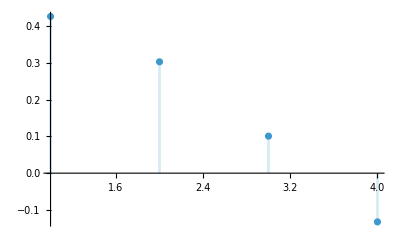

```mathematica
DiscretePlot[g0[n]//N,{n,40}]
DiscretePlot[logg0[n]//N,{n,40}]
DiscretePlot[logg0[n]//N,{n,4}]
```

```mathematica
PP=Plot[Evaluate[{Sigma[5,0,W Ry,1],Sigma[10,0,W Ry,1],Sigma[20,0,W Ry,1]}], {W, 0, 0.02},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, {0,14*10^-17}}]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-9829.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export["Exports/DT_M5s10s20s_v3.png",PP, "png",ImageResolution -> 300]
```

Exports/DT_M5s10s20s_v3.png

```mathematica
eE0=Sqrt[h];
Ei[i_]:=-Ry/i^2;
ωi[i_]:=Ei[i]/h;
(*T[w_]:=100;*)
SumPWOmega2up[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[((l+1)^2-m^2)/(4(l+1)^2-1),{m,-l,l}]* Abs[gup[n-l][n, Sqrt[W/Ry]]]^2;
SumPWOmega2down[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[(l^2-m^2)/(4l^2-1),{m,-l,l}]* Abs[gdown[n-l][n, Sqrt[W/Ry]]]^2;
```

```mathematica
sincTerm[W_, ω_,i_,T_] := Sinc[((W- Ei[i])/h - ω)/2 * T]^2
```

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[1]/h;
```

Case 1

```mathematica
integrand[W_, ω_,T_] :=  T^2/(2*hbar^2) (SumPWOmega2up[1, 0, W]sincTerm[W, ω,1,T]+SumPWOmega2up[2, 0, W]sincTerm[W,ω,2,T])

Pni[ω_?NumericQ, T_?NumericQ] := NIntegrate[integrand[W, ω,T], {W, 0, (ω+10*2Pi/T)h}]
```

```mathematica
(* Plot range *)

data1 = Table[{ω, Pni[ω,-8Pi h/Ei[1]]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
(*Export["Pni_data_M=2T=100_v0.wl", data, "WL"];  Wolfram Language format *)
```

```mathematica
Ei[1]/4
```

-5.44968×10^-19

```mathematica
Plot[integrand[0,ω,-8Pi h/Ei[1]], {ω, ωmin,ωmax}]
```

-Graphics-

```mathematica
Plot[integrand[W,-Ei[1]/h,-8Pi h/Ei[1]], {W, 0, (ωmax)h},PlotRange ->{Automatic,Automatic}]
```

General::munfl: Exp[-1135.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
(* Plot Pni(ω) *)
P = Labeled[
  ListPlot[data1, 
 ImageSize -> 600,Joined -> True],
  Style["ω",  FontSize -> 20],
  Bottom
]
```

-Graphics-ω

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export["Exports/IP_M1s2sT=E1by4E0e=sqrth_v3.png",P, "png",ImageResolution -> 300]
```

Exports/IP_M1s2sT=E1by4E0e=sqrth_v3.png

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[0];
data2 = Table[{ω, Pni[ω,1000]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
Export["Pni_data_M=2_v0.wl", data2, "WL"]; (* Wolfram Language format *)
```

```mathematica
ListLogPlot[data2, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 GridLines -> Automatic,
 ImageSize -> 600,Joined -> True,
Epilog->Table[{Gray, Dashed, Line[{{1/(2*i^2), 0}, {1/(2*i^2), 40000}}]},{i,M}]] (* Control recursion depth *)
```

-Graphics-

```mathematica
(* Constants and Parameters *)
i = 2;                     (* Defined i *)
Ei =- 1/(2*i^2);             (* Defined E_i *)
Γ23 = Gamma[2/3];          (* Gamma function *)
T[ω_] := 100;             (* T depends on omega *)
E0e = 1;

(* Prefactor term - using En instead of E to avoid conflict *)
prefactor[En_] := 1

(* Sinc-squared term *)
sincTerm[En_, ω_] := Sinc[(En - Ei - ω)/2 * T[ω]]^2

(* Full integrand *)
integrand[En_, ω_] := 1 * prefactor[En] * sincTerm[En, ω]

(* Numerical integration for Pni(ω) *)
Pni[ω_?NumericQ] := NIntegrate[integrand[En, ω], {En, 0, ∞}]

(* Plot range *)
ωmin = 0;
ωmax = -2*Ei;

(* Plot Pni(ω) *)
Plot[Pni[ω], {ω, ωmin, ωmax}, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 PlotRange -> All,
 GridLines -> Automatic,
 PlotPoints -> 30, (* Increase sampling for smoother plot *)
 MaxRecursion -> 3] (* Control recursion depth *)
```

-Graphics-